# Data Analytics

## Interactive Visualisation, Probabilistic Modelling, and Machine Learning with Mathematica

-Graphics-

Poomjai Nacaskul, Ph.D.

Applied Digital Intelligence
		Chulalongkorn School of Integrated Innovation

Prologue

This textbook grew out of a practical need and a personal conviction.

On the one hand, I needed to develop a set of interactive learning materials for my Data Analytics lectures at the Chulalongkorn School of Integrated Innovation (CSII)’s Bachelor of Arts and Science in Integrated Innovation (BAScii) programme.

On the other hand, I am thoroughly convinced that learning mathematics in particular, technical-scientific subjects in general, can be made easy and a lot of fun if learners can visualise and interact (hence interactively visualise) the mathematical functions, theoretical and/or empirical relationships themselves.

I recall back to my undergraduate years at Western Reserve College, Case Western Reserve University (CWRU), probably as a freshman and a year or so before I eventually declared my double majors (Physics & Economics), thinking there has got to be a software to help students intuit the famous IS-LM curve in Macroeconomics.

Shortly after, while at CWRU Weatherhead School of Management’s Operations Research M.S. degree programme, taking classes in Linear Programming (LP) and Nonlinear Programming (NLP) probably only served to deepen my conviction: if only students could interactively visualise the Simplex Algorithm and Karush-Kuhn-Tucker conditions for themselves.

Then it was off to Imperial College London. One of my co-supervisors, and a legend in her own time, the late Professor (then Reader) Antonia J. Jones [https://en.wikipedia.org/wiki/Antonia_J._Jones] pushed me onto what I believe was Mathematica 5. This was around the time she was excitedly fleshing out the techniques and applications of the so-called “Gamma Test”, an elegant, continuity-inspired algorithm that effectively placed upper bound on determinism, hence predictability, that can be captured by any and all, indeed the theoretical best-possible, Machine Learning (ML) algorithms. Unfortunately, and this is possibly one of my lifelong regrets, I didn’t embrace the opportunity. My Ph.D. thesis “Evolutionary Optimisation and Financial Model-Trading” applied Object-Oriented Paradigm to the representation of my modular ensemble of financial trading models as evolutionary agents and so C++ was, I insisted, the way to go. For all its analytical prowess, Mathematica would have been but a distraction.

Several years went by, whilst enjoying my career knees deep in Quantitative Finance as an analyst at the Bank of Thailand (Thailand’s Central Bank), I came upon Copula research, and got inspired to “nonlinearise” the dependence relation. My hands were tied. I needed an analytical engine! I turned to Mathematica, whereupon it my formulation led to Mathematica spewing out “Kummer’s Confluent Hypergeometric Function”, which I could not come up with in on my own in a million years, and I was hooked. This ended being my invention of the “Gaussian Slug” distribution and copula, partially introduced in Chapter 4 on Probabilistic Modelling.

Then from central banking to commercial banking, I found myself tasked with helping a team validate an “exotic” Foreign Exchange (FX) Options model. Mathematica, with the analytical differentiation and equation solving capabilities, once again came to my rescue.

Then came Big Data, Data Science, and Data Analytics. Many of my colleagues were writing Python boilerplates and losing sleeps with Mathplotlib. Meanwhile, 6 generations later, Mathematica 11 had, well, just about everything (well, everything but the largest pre-trained models). In particular, exploiting Mathematica for its scientific-mathematical visualisation and user-learner interactivity forms the very premise of this textbook.

Then from central banking to commercial banking, I found myself tasked with helping a team validate an “exotic” Foreign Exchange (FX) Options model. Mathematica, with the analytical differentiation and equation solving capabilities, once again came to my rescue.

Preface

I originally envisioned this as, in the terminology of the Wolfram ecosystem, a Computable Document Format (CDF). Indeed it is written as a Mathematica notebook (.nb) file, which could just as easily be saved as a “.cdf” file. After a few years experimenting with teaching Data Analytics at the undergraduate level, my thinking changed. Yes, ultimately I should like the students to have all the words and all the codes. But students should have to manually write in the codes themselves! Giving them codes to Shift + Enter will ultimately shortcut their learning process! Hence, good old-fashioned static pages and pages of words, pictures, and example codes is the what I have decided to go with.

As a textbook proper, there should be, in addition to the main body of text, end-of-chapter exercises (perhaps solution books for lecturers/teacher assistants), glossary, reference/bibliography, etc. This textbook is incomplete in that sense. With Data Analytics, exercises are best done with real data, so I refer to the vast GitHub repository for that purpose. There is a small glossary at the end, but my intention is not so much to provide a comprehensive list of terms as to clarify the confusions that confound a couple of popularised terms in the space of Data Science, Machine Learning, Artificial Intelligence, etc. Finally, this textbook is meant as an exposition on the already ubiquitous tools and techniques in the world of Data Analytics, hence readers are better served being referred to either Mathematica resource pages or Wikipedia entries.

This interactive textbook is meant to be largely self-contained. Additional resources as well as example (input) data files can be downloaded from the author’s GitHub.

https://github.com/PoomjaiNacaskul/DataAnalytics

```mathematica
(* Misc. Display Defaults/Utilities *)
DateObject[LocalTime[],"Day"]
SetDirectory[NotebookDirectory[]];
𝒯𝒶𝒷ℓℯ[heading_,table_,
alignment_:Automatic,frame_:All,sideway_:False]:=
Grid[If[sideway,
Transpose@Prepend[table,Style[#,Bold,RGBColor[0,0,1]]&/@heading],
Prepend[table,Style[#,Bold,RGBColor[0,0,1]]&/@heading]],
Alignment->alignment,Frame->frame]
ℐ𝓃𝒻ℴ𝒟[𝒟_,x_,
alignment_:Automatic,frame_:All,sideway_:False]:=
𝒯𝒶𝒷ℓℯ[{"pdf/pmf","Mean","Variance","Skewness","Kurtosis"},
{TraditionalForm/@{PDF[𝒟,x],Mean[𝒟],Variance[𝒟],Skewness[𝒟],Kurtosis[𝒟]}},
alignment,frame,sideway]
ℋ𝒾𝓈𝓉ℴℊ𝓇𝒶𝓂[data_,
spec2_:"PDF",spec1a_:Automatic,spec2b_:Automatic,
element_:"GlassRectangle",style_:"Pastel",
filling_:None,rangePlot_:All]:=
Show[
Histogram[data,spec1a,spec2,ChartElementFunction->element,ChartStyle->style],
SmoothHistogram[data,spec2b,spec2,Filling->filling,PlotRange->rangePlot]]
GRAPHLAYOUT={Automatic,
Delimiter,"CircularEmbedding","GridEmbedding",
"MultipartiteEmbedding","SpiralEmbedding","StarEmbedding",
Delimiter,"BalloonEmbedding","RadialEmbedding",
"LayeredDigraphEmbedding","LayeredEmbedding",
Delimiter,"GravityEmbedding","HighDimensionalEmbedding",
"SpectralEmbedding","SpringElectricalEmbedding",
"SpringEmbedding","TutteEmbedding"};
SetOptions[{Plot,Plot3D,SmoothHistogram,SmoothHistogram3D,
ContourPlot,ContourPlot3D},PlotRange->All];
SetOptions[{Plot,SmoothHistogram},Filling->Axis];
SetOptions[{Histogram,BarChart},
ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel"];
SetOptions[Manipulate,ControlPlacement->Bottom];
```

Mon 12 Aug 2024

2

## Chapter 2 - Intro to Wolfram Mathematica

This chapter is organised into two parts. The first part explores Mathematica as the scientific computation platform as originally intended and ever since evolved over the years. The second part delves into the Wolfram programming language itself, the basics necessary to begin coding as well as the mathematical/symbolic/analytical functionalities not available to general programming language, the likes of C, Java, or Python, and so on.

Intro to Mathematica (the Scientific Computation Platform)

Evolution of Mathematica

www.wolfram.com/mathematica

Mathematica 1.0

https://writings.stephenwolfram.com/2013/06/there-was-a-time-before-mathematica

Mathematica 1.0 was released in June 1988. Long story short, a theoretical high-energy physicist by the name of Dr. Stephen Wolfram set out to create a symbolic programming language to help himself "do physics". Many, many years later his creation ended up powering a great deal of scientific discoveries, not just in Physics, but much more, in Artificial Intelligence, Biology, Cybernetics, Data Science, Engineering, Finance, Genetics, Hydrology, Information Theory, Kinematics, Linguistics, Mathematics, Neuroscience, Oceanography, Quantum Computing, Robotics, Statistics, Tectonics, and the list just goes on and on.

In his own words ...

"... in the summer of 1977 I discovered the ARPANET, or what's now the internet. There were only 256 hosts on it back then. And @O 236 went to an open computer at MIT that ran a program called Macsyma—that did algebra, and could be used interactively. I was amazed so few people used it. But it wasn't long before I was spending most of my days on it. I developed a certain way of working—going back and forth with the machine, trying things out and seeing what happened. And routinely doing weird things like enumerating different algebraic forms for an integral—then just "experimentally" seeing which differentiated correctly.

My physics papers started containing all sorts of amazing formulas. And not imagining that I could be using a computer, people started thinking that I must be some kind of great human algebraic calculator. I got more and more ambitious, trying to do more and more with Macsyma. Pretty soon I think I was its largest user. But sometime in 1979 I hit the edge; I'd outgrown it.

... November 1979. I was 20 years old, and I'd just gotten my PhD in physics. I was spending a few weeks at CERN, planning my future in (as I believed) physics. And one thing I concluded was that to do physics well, I'd need something better than Macsyma. And after a little while I decided that the only way I'd really have a chance to get what I wanted was if I built it myself.

And so it was that I embarked on what would become SMP (the "Symbolic Manipulation Program"). I had a pretty broad knowledge of other computer languages of the time, both the "ordinary" ALGOL-like procedural ones, and ones like LISP and APL. At first as I sketched out SMP, my designs looked a lot like what I'd seen in those languages. But gradually, as I understood more about how different SMP had to be, I started just trying to invent everything myself.

... late in August 1986, I decided to try to build my ultimate computation system—that could do all the computations I wanted, or could imagine I would ever want.

And of course the result was Mathematica.

... The first code for Mathematica was written in October 1986. And by the middle of 1987 Mathematica was beginning to come to life. I'd decided that the documentation should be published as a book, and hundreds of pages were already written. And I estimated that Mathematica 1.0 would be ready by April 1988.

... Steve Jobs was the first to take Mathematica on, making a deal to bundle it with every one of his as-yet-unreleased NeXT computers. Deals with Sun, Silicon Graphics, IBM and a sequence of other companies followed.

... Sometime in the spring of 1988, we officially set June 23 as the release date for Mathematica (without Wolfram|Alpha, I didn't know it was Alan Turing's birthday, etc.)."

[Stephen Wolfram (2013), "There Was a Time before Mathematica…",  https://writings.stephenwolfram.com/2013/06/there-was-a-time-before-mathematica ].

Mathematica Notebook

https://reference.wolfram.com/language/guide/ManagingComputationsInNotebooks.html

Notebook Kernel

As a coding/development platform, Mathematica Notebook broke new grounds. One key feature is the notion and implementation of code "kernels", an idea supposedly taken up and employed just a few years later by the creator of Jupyter Notebook for Python programming.

Start the Mathematica program, type in 1 + 1 and Shift + Enter.

```mathematica
1+1
```

2

Notice the appearance of 'In[ ]' and 'Out[ ]' cells or kernels. Different lines in 'In[ ]' corresponds to different 'Out[ ]' cells. A semicolon ';'  silences the output. It is also used to separate multiple commands.

```mathematica
1;2
3+4;5
```

2

5

Depending on "In[ ]struction", "Out[ ]put" can contain many things beside just numbers.

```mathematica
Blue
```

RGBColor[0, 0, 1]

```mathematica
𝒯𝒶𝒷ℓℯ[{"Caffeine","Fluoxetine"},
{{Show[ChemicalData["Caffeine","MoleculePlot"],ImageSize->Small],
Show[ChemicalData["Fluoxetine","MoleculePlot"],ImageSize->Small]}}]
```

Caffeine | Fluoxetine
-Graphics3D- | -Graphics3D-

At times, 'Out[ ]' simply reports an internal "system state", such as when an internal Pseudo Random Number Generator (PRNG) is seeded.

```mathematica
SeedRandom[1234]
```

RandomGeneratorState[…]

Recall Previous Cell

https://reference.wolfram.com/language/ref/Out.html

Entering '%' recalls the previous output, '%%' recalls the one before that, and so on, and '%' followed by an earlier line number recalls the correspondingly-numbered output (even if it had earlier been silenced by ';').

```mathematica
%%%
```

RGBColor[0, 0, 1]

Free-Form Linguistic Input

www.wolfram.com/mathematica/new-in-8/free-form-linguistic-input

Introduced in November 2010, Mathematica 8.0, in a move closer to user-friendly Declarative Programming paradigm, provided Free-Form Linguistic Input. In this mode one can just type '=' once, followed by natural language prompt indicating the desired outcome, and the software would try to respond with the appropriate Mathematica command suggestion, filling the template with initial parameters that users can of course specify to suit. Having said that, all but absolute beginners tend to find auto-complete pop-ups generally suffice, many finding free-form linguistic input mode tends to distract/disrupt workflow. Note the "placeholder" cell for users to specify input.

WolframAlphaQueryParseResults

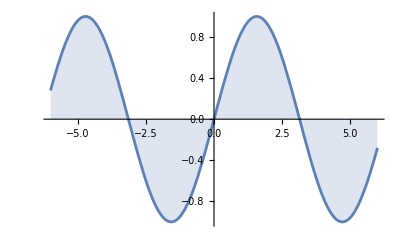

```mathematica
Plot[Evaluate[Sin[x]], {x, -6., 6.}]
```

Mathematica 14

www.wolfram.com/mathematica/quick-revision-history.html

January 2024 saw the release of Mathematica 14, which is the current version. From our perspective, however, amongst the most interesting milestones were the introduction of Dynamic Interactivity in version 6, comprehensive Statistical Distribution library in version 8, GPU-powered Neural Networks/Machine Learning algorithms and Geo-Data Visualisation/Computation in version 11, Natural Language Processing engine and Bio-Medical object models in version 12.

Mathematica in Context

Programming Paradigm

Functional Programming

https://reference.wolfram.com/language/guide/FunctionalProgramming.html

Wolfram Mathematica is primarily a Functional Programming language, which is to say that it best suits, and is best described by, this paradigm than, say, Procedural Programming or Object-Oriented Programming. Of course, procedural constructs like For/Do/While loops exist, and there have been efforts to embed Mathematica with object-oriented architecture, but writing Mathematica codes in such manner has a very "unnatural feel" about it.

With functional programming, the main modality with which the programmer interacts with the computer is by breaking down tasks into series of function calls. Each function can be thought of as a manufacturing station, taking in the inputs (function arguments), doing something with them (the mathematical mapping functionality itself), and providing the outputs (function values). Outputs from one function then become input to another function, and so on. The task of programming comprises of defining a new function from a number of functions defined earlier (built-in as part of the language or similarly user-defined), and coordinating a series of function calls, often referred to as algorithmic "pipelines".

Declarative Programming

Having said that, one may argue that because Mathematica, while capable of heavy-duty computational and analytical tasks, presents itself as a very high-level language, that is, hiding much of parametric specification detailing through the use of default arguments, etc., Mathematica at time feels very much of a Declarative Programming camp (especially with free-form linguistic input mode). One essentially "tells" the software what needs to be done, plot data, perform statistical tests, build neural networks, whatever, and it's done. From there, "power users" would naturally delve deeper and customise the functionalities to suit, as "rough and ready" results that first appear aren't likely to be exactly what they have in mind.

Wolfram's "Computational Intelligence" Platform

In the Wolfram universe, the term "Computational Intelligence" revolves around/emerges from the evolution of Mathematica from the scientific computing origin to the aspiration of endowing/empowering "all of humanity's knowledge base" with advanced quantitative analytics.

This rather noble/ambitious enterprise probably starts with how Mathematica aims to treat all matters of things as if they were intrinsically/covertly "computable objects". In a matter of speaking, if one could somehow define an "algebra of fruits", then Mathematica would be able to perform calculations on them.

Generalised Entity Types

https://reference.wolfram.com/language/guide/EntityTypes.html

Wolfram Alpha

www.wolframalpha.com

Whereas Wolfram Mathematica is fundamentally a programming language, furnished with massive/growing built-in function library, Wolfram Alpha, introduced with Mathematica 7.0 in November 2008,  is an interactive knowledge base. Imagine doing a Google or Wikipedia search, except the search results can then be interactively visualised, statistically tested, symbolically analysed, numerically computed, and/or machine learned. Likewise, when one queries a large language model like ChatGPT, responses are formed out of associative memory, 2 + 2 = 4 because 4 is associated with 2 + 2, and such responses are accurate for much more complicated mathematical operations, but if ChatGPT is "backend-pipelined" to Wolfram Alpha, then such responses would be based in outputs from analytical engines proper, whence 2 + 2 = 4 not by association but by traditional digital computer.

To prompt a Wolfram Alpha inquiry in Mathematica Notebook, just type '=' twice, followed by whatever search term.

Solar Eclipse

WolframAlphaQueryResults

Large Language Model (LLM) with Wolfram Plugin

www.wolfram.com/wolfram-plugin-chatgpt

Science, Engineering & Industry

Scientific Data Analysis & Machine Learning

Although this book is written precisely on this subject, Mathematica's own online learning resource is itself an excellent and comprehensive self-learning platform.

https://reference.wolfram.com/language/guide/ScientificDataAnalysis.html

https://reference.wolfram.com/language/guide/MachineLearning.html

www.wolfram.com/resources/tools-for-AIs

Optimisation & Control Systems

As this subject is beyond the scope of this book, we recommend Mathematica's own online learning resource as an excellent self-learning platform.

https://reference.wolfram.com/language/guide/Optimization.html

https://reference.wolfram.com/language/guide/ControlSystems.html

https://reference.wolfram.com/language/tutorial/ConstrainedOptimizationOverview.html

Scientific Computing & Industrial Solutions

As this subject is beyond the scope of this book, we recommend Mathematica’s own online learning resource as an excellent self-learning platform.

www.wolfram.com/solutions

https://reference.wolfram.com/language/guide/ScientificModels.html

https://reference.wolfram.com/language/guide/SystemsModeling.html

Software Ecosystem

Curated Datasets/Entity Databases

```mathematica
ExampleData[]
```

{AerialImage,Audio,ColorTexture,Dataset,Geometry3D,LinearOptimization,LinearProgramming,MachineLearning,Matrix,NetworkGraph,Sound,SpatialPointData,Statistics,TestAnimation,TestImage,TestImage3D,TestImageSet,Text,Texture}

Here we see that there are altogether 19 types of data objects (i.e. the "V for Variety" and the last of the  3 Vs of Big Data, the other two being "V for Volume"  and "V for Velocity"). Suppose we focused on the mainly numerical "Statistics" datasets. Here we see that there are 111 datasets under this heading alone.

```mathematica
ExampleData["Statistics"]//Length
```

111

Let’s randomly pick out 20 datasets.

```mathematica
SeedRandom[1234];
RandomSample[ExampleData["Statistics"],20]
```

{{Statistics,ChemicalProcessTemperatures},{Statistics,FisherIris},{Statistics,CrabMeasures},{Statistics,IndomethicinPharmacokinetics},{Statistics,AnimalWeights},{Statistics,BatchChemicalProcessYields},{Statistics,NickelContent},{Statistics,FisherCats},{Statistics,USCars1993},{Statistics,EconomicFluctuation},{Statistics,CementHeat},{Statistics,BirthWeightRisk},{Statistics,USArrests},{Statistics,BeaverBodyTemperatures},{Statistics,Formaldehyde},{Statistics,Cushings},{Statistics,SoporificDrugs},{Statistics,BlackCherryTrees},{Statistics,OzoneConcentrations},{Statistics,BiochemicalOxygenDemand}}

Going beyond example datasets, professional chemists, for instance, would have well over 40 thousands molecular data to work with.

```mathematica
Length[ChemicalData[]]
```

44089

```mathematica
RandomSample[ChemicalData[],20]
```

{phenylmaleic anhydride,triethylhexylammonium bromide,tri-O-acetyl-β-D-arabinosylbromide,disodium fumarate,3-butenylamine hydrochloride,ga13,3-phenylpropionyl-CoA,2,4(3H,5 H)-furandione,amo-1618,5-(4-methoxyphenyl)-2-furoic acid,strictosidine-aglycone,guanosine 5'-diphosphate 2':3'-cyclic monophosphate,chloropentafluoroethane,6-hydroxyhexanoate,bis[2-(methacryloyloxy)ethyl]phosphate,lithium iodate,2-chloro-4-(trifluoromethoxy)aniline,allyl isocyanate,dimethyl(S)-(-)-malate,2'-aminoacetanilide}

Software Prototype/Development/Deployment Platform

https://reference.wolfram.com/language/workflow/CreateInteractiveContentForTheWeb.html

The powerful computational, analytical engines, combined with interactive visualisation, makes Wolfram Mathematica a natural tool for software development in general, proof-of-concept prototyping in particular.

A well-proven workflow is for the mathematics and application concepts to be worked out, expressed/computed/visualise using Mathematical functions first. Once these are thoroughly worked out, more practical deployment options can be considered.

Nowadays this often means Python infrastructure with some kind of web application tools. Of course, it is important to be mindful of what is possible in Mathematica but not doable down line. For example, a closed-form analytical integration may be demonstrated in Mathematica, but Python deployment will have to rely on numerical approximation for results.

For example, calculating a factorial in Mathematica would have to be translated as numerical approximation of a Gamma function in some Python library, and so on. For practical applications, this generally suffices.

https://reference.wolfram.com/language/guide/WebOperations.html

As running a Mathematica program requires software licences, demonstrating the Mathematica-developed application/prototype can restrict the potential audience. Here are two ways of getting around this.

www.wolfram.com/player

The first way is for the client/audience can download the "player" and play pre-written Mathematica scripts saved as "Computable Document Format" files. This enables the client/audience to interactively explore the functionalities provided by the Mathematica-developed application/prototype.

https://reference.wolfram.com/language/ref/CloudDeploy.html

The second way is to CloudDeploy[ ] Mathematica output and provide the client/audience with the URL. This is the more "portable" method of the two, but beware that computationally intensive routines can take a while as cloud-deployed objects.

```mathematica
SeedRandom[1234];
Module[{rgb=RGBColor[.3,.5,.7]},
Manipulate[
Graphics[{rgb,Disk[]},ImageSize->Small],
Style["Your Lucky Tone Today",Medium,Bold],
Button["Red",rgb=RGBColor[RandomReal[{.5,1}],RandomReal[.25],RandomReal[.25]]],
Button["Green",rgb=RGBColor[RandomReal[.25],RandomReal[{.5,1}],RandomReal[.25]]],
Button["Blue",rgb=RGBColor[RandomReal[.25],RandomReal[.25],RandomReal[{.5,1}]]],
ControlPlacement->Right]]
CloudDeploy[%,Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/a060469c-51d9-4d67-b2f3-f5cbd983bb41]

Wolfram Learning Resources/Demonstrations Projects/Community

www.wolfram.com/mathematica/resources

https://demonstrations.wolfram.com

https://community.wolfram.com

Despite many advantages of Mathematica, its ecosystem is decidedly miniscule especially when compared to the ginormous Python ecosystem. To quote ChatGPT on relative merits of Mathematica over Python (query date 2023.06.19):

"Comparing Wolfram Mathematica and Python is not a straightforward task, as they have different strengths and use cases. Here are some aspects where Mathematica may be considered advantageous over Python:

1. Symbolic Computation: Mathematica is renowned for its symbolic computation capabilities, allowing it to handle mathematical equations, calculus, and symbolic manipulation with ease. It can work with exact numbers, arbitrary precision arithmetic, and advanced mathematical functions out of the box.

2. Integrated Environment: Mathematica offers a fully integrated development environment with a notebook interface that combines code, documentation, and visualizations in a single interface. It provides a cohesive environment for exploratory programming, prototyping, and interactive data analysis.

3. Built-in Functions and Algorithms: Mathematica includes an extensive collection of built-in functions and algorithms for various domains, such as mathematics, statistics, data analysis, visualization, and more. This comprehensive set of functionality can save time and effort when working on diverse computational tasks.

4. Natural Language Input and Wolfram|Alpha Integration: Mathematica allows natural language input, enabling users to express computations and queries in plain English. Additionally, it integrates with Wolfram|Alpha, providing access to vast amounts of curated data, computations, and knowledge.

5. Wolfram Language: Mathematica uses the Wolfram Language, a powerful and high-level programming language specifically designed for symbolic and numerical computations. The language is built into Mathematica, offering a consistent and unified approach to various tasks.

That said, Python has its own strengths, including a vast ecosystem of libraries, widespread adoption, versatility, and excellent support for general-purpose programming. Python's extensive library support makes it well-suited for tasks such as web development, machine learning, scientific computing, and data analysis, where it often has a larger and more specialized ecosystem compared to Mathematica.

Ultimately, the choice between Mathematica and Python depends on the specific requirements of your project, your programming preferences, and the nature of the tasks you need to accomplish."

Intro to Wolfram (Mathematica Programming Language)

Language Syntax/Programming Primitives

www.wolfram.com/language

Assignment

https://reference.wolfram.com/language/guide/Assignments.html

In Mathematica, the equality sign is used strictly as an assignment operation, i.e. the variable left-hand-side of the sign is assigned to mean whatever appears as value on the right-hand-side. Note that prior to assignment, the variable is "unknown" to Mathematica, hence the characters appear in blue. Once assigned to something, the variable is "known" to Mathematica, hence the characters turn black in appearance, i.e. same as any other built-in language objects (functions, constants, and numbers). The assignment remains so throughout session, and its value is fixed across program instances. That is, once Mathematica software is launched, different program codes will share the same variable and function definitions. In other words, definitions are, by default, global.

```mathematica
x=1
```

1

```mathematica
x=123;
x
```

123

```mathematica
x=x-111;x/=3
```

4

To avoid needless confusion later on, it is a good practice to apply Clear[ ] to all such assignment(s) immediately after use. Note: there will be a better, more elegant way of defining the scope of assignment, i.e. using Module[ ].

```mathematica
Clear[x]
```

In mathematics, an assignment is generally between a named variable on the left-hand side and the assigned value on the right-hand side. In Mathematica, however, assignment is best thought of as a general process of naming, whence allowing later reference to the "right-hand side" by its name as indicated on the "left-hand side". As per functional programming paradigm, what gets named is often not so much a variable as it is a function.

https://reference.wolfram.com/language/guide/VariablesAndFunctions.html

One can even define a function, then a partial differential equation and name it via assignment operator ‘=’.

```mathematica
heatFunc=u[x,t];
heatEqn=D[heatFunc, t]==D[D[heatFunc, x], x];
𝒯𝒶𝒷ℓℯ[{"1D Heat Function","1D Heat Equation"},
{TraditionalForm/@{heatFunc,heatEqn}},Left]
```

1D Heat Function | 1D Heat Equation
u(x,t) | u^(0,1)(x,t)==u^(2,0)(x,t)

```mathematica
Clear[heatFunc,heatEqn]
```

List

Definition

https://reference.wolfram.com/language/guide/ListManipulation.html

In Mathematica, List[ ] is an ordered sequence of objects, not necessarily of the same type, denoted with '{' a the beginning, '}' at the end, and ',' for separation between items. Lists are often constructed by way of functions, but one can of course manually list all the elements, either with the explicit function List[ ], or simply (and more often) with the brackets themselves.

```mathematica
List[a,b,c]
```

{a,b,c}

```mathematica
z={12,Blue,"Boats"}
```

{12,RGBColor[0, 0, 1],Boats}

Accessing Individual Item(s)

Each item in a list can be individually accessed (fetched) via its index (position number) using double square bracket '[[ ]]'.

```mathematica
z[[1]]
z[[-1]]
```

12

Boats

A negative index means one should start counting from the last (right-most) item.

To access more than just one elements, using ';;' to separate the 'first-to-fetch' from the 'last-to-fetch'. If 'first-to-fetch' is left unspecified, first item in the list is assumed. If 'last-to-fetch' is left unspecified, last item in the list is assumed.

```mathematica
z[[;;2]]
z[[2;;]]
```

{12,RGBColor[0, 0, 1]}

{RGBColor[0, 0, 1],Boats}

Note that ';;' is the same as 'All'.

```mathematica
z==z[[;;]]==z[[All]]
```

True

Alternatively, a list of indices can be used to specify items to fetch.

```mathematica
z[[{-3,1,-2,2,-1,3}]]
```

{12,12,RGBColor[0, 0, 1],RGBColor[0, 0, 1],Boats,Boats}

```mathematica
Clear[z]
```

List of Lists

Each item in a list can itself be a list. A list of lists with same number of elements resembles a rectangular array.

```mathematica
rgb={{"R","G","B"},{Red,Green,Blue}}
```

{{R,G,B},{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}}

For a list of lists, two indices are needed to access (fetch) individual elements.

```mathematica
rgb[[2,1]]
```

RGBColor[1, 0, 0]

One index just fetches a single row.

```mathematica
rgb[[2]]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

Or a single column, if provided ';;' or 'All' is indicated as row reference.

```mathematica
rgb[[All,2]]
```

{G,RGBColor[0, 1, 0]}

Note that using two indices to access an element from a list of lists can be thought of as a “shorthand” for accessing its element, which itself is a list, and then accessing its element.

```mathematica
rgb[[2,1]]==rgb[[2]][[1]]
```

True

Function

https://reference.wolfram.com/language/tutorial/FunctionalOperations.html

Technically speaking, just about Mathematica input is a function call. In mathematics, writing f(x) means one is calling the function f, supplied with argument x. In Mathematica, this would be denoted f[x], with '[' a the beginning, 'x' in the middle, and ']' at the end (i.e. square bracket instead of round).

Prompt

A pure prompt calls a function that cannot be supplied with an argument. This is rarely used.

```mathematica
Now
```

Mon 12 Aug 2024 16:12:38GMT+7

```mathematica
Tomorrow
```

Tue 13 Aug 2024

Command

A command calls a function that is supplied with no argument, even though there could be one or more pre-defined default argument(s).

```mathematica
NotebookDirectory[]
```

C:\Users\Poomjai\Documents\PNacaskul\PoomWorks3.2\(2006-2024) LectureNotes&Texts\(2024.08.10) Data Analytics - Interact Visual, Prob Model & Machine Learning\

Univariate Function

Univariate Function - Functional Programming Notation

```mathematica
Exp[12.34]
```

228662.

```mathematica
Dimensions[rgb]
```

{2,3}

Here is a univariate function used to prime-factor a (reasonably) large number, hence calling up some algorithmic calculations "behind the scene".

https://reference.wolfram.com/language/ref/FactorInteger.html

```mathematica
FactorInteger[29192]
```

{{2,3},{41,1},{89,1}}

Let’s verify.

```mathematica
2^3 41 89
```

29192

On the other hand, some functions are used for "formatting" rather than for performing calculation.

https://reference.wolfram.com/language/ref/TraditionalForm.html

https://reference.wolfram.com/language/ref/InputForm.html

TraditionalForm[ ] displays mathematical expressions as if in traditional text books, while InputForm[ ] does the opposite.

```mathematica
TraditionalForm[Integrate[f[x],{x,a,b}]]
InputForm[%]
```

∫_a^b f(x)ⅆx

Integrate[f[x], {x, a, b}]

Of course, an input variable needs not be scalar.

```mathematica
{Norm[{1,1}],Norm[{3,4}],Norm[{5,12}],
Total[{3,9,2,8,6,7,0}],Mean[{3,1,0,0,9,0,1,7,9,5}]}
```

{√2,5,13,35,7/2}

Here are examples of useful "formatting" univariate functions supplied with list arguments.

https://reference.wolfram.com/language/ref/TableForm.html

TableForm[ ] helps display a list (of lists) in tabular "rows-and-columns" format.

```mathematica
𝒯𝒶𝒷ℓℯ[{"TableForm[rgb]","TableForm[{a_1,a_2,a_3}]","TableForm[{{a_1,a_2,a_3}}]","TableForm[{{a_1},{a_2},{a_3}}]"},
{TableForm/@{rgb,{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}},{{Subscript[a, 1]},{Subscript[a, 2]},{Subscript[a, 3]}}}}]
```

TableForm[rgb] | TableForm[{a_1,a_2,a_3}] | TableForm[{{a_1,a_2,a_3}}] | TableForm[{{a_1},{a_2},{a_3}}]
R | G | B
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | a_1
a_2
a_3 | a_1 | a_2 | a_3 | a_1
a_2
a_3

https://reference.wolfram.com/language/ref/MatrixForm.html

MatrixForm[ ] displays a list as a mathematical vector, a list of (equal-length) lists as a mathematical matrix, and a list of (equal-length) lists of (equal-length) lists as a mathematical tensor.

```mathematica
𝒯𝒶𝒷ℓℯ[{"vector: a ∈ ℛ^3","row vector: a ∈ ℛ^(1×3)","column vector: a ∈ ℛ^(3×1)"},
{MatrixForm/@{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},{{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]}},{{Subscript[a, 1]},{Subscript[a, 2]},{Subscript[a, 3]}}}}]
```

vector: a ∈ ℛ^3 | row vector: a ∈ ℛ^(1×3) | column vector: a ∈ ℛ^(3×1)
(a_1
a_2
a_3) | (a_1 | a_2 | a_3) | (a_1
a_2
a_3)

```mathematica
Dimensions[a2X3={{Subscript[a, 11],Subscript[a, 11],Subscript[a, 11]},{Subscript[a, 12],Subscript[a, 12],Subscript[a, 12]}}]
Dimensions[a2X2X3={{{Subscript[a, 111],Subscript[a, 112],Subscript[a, 113]},{Subscript[a, 121],Subscript[a, 122],Subscript[a, 123]}},{{Subscript[a, 211],Subscript[a, 212],Subscript[a, 213]},{Subscript[a, 221],Subscript[a, 222],Subscript[a, 223]}}}]
Dimensions[rgb2X2={{{Subscript[r, 11],Subscript[g, 11],Subscript[b, 11]},{Subscript[r, 12],Subscript[g, 12],Subscript[b, 12]}},{{Subscript[r, 21],Subscript[g, 21],Subscript[b, 21]},{Subscript[r, 22],Subscript[g, 22],Subscript[b, 22]}}}]
```

{2,3}

{2,2,3}

{2,2,3}

```mathematica
𝒯𝒶𝒷ℓℯ[{"rgb \"2×3-pixel screen\"","matrix: A ∈ ℛ^(2×3)","tensor: T ∈ ℛ^(2×2×3)","tensor: rgb ∈ [0,1]^(2×2×3)"},
{MatrixForm/@{rgb,a2X3,a2X2X3,rgb2X2}}]
```

rgb "2×3-pixel screen" | matrix: A ∈ ℛ^(2×3) | tensor: T ∈ ℛ^(2×2×3) | tensor: rgb ∈ [0,1]^(2×2×3)
(R | G | B
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]) | (a_11 | a_11 | a_11
a_12 | a_12 | a_12) | ((a_111
a_112
a_113) | (a_121
a_122
a_123)
(a_211
a_212
a_213) | (a_221
a_222
a_223)) | ((r_11
g_11
b_11) | (r_12
g_12
b_12)
(r_21
g_21
b_21) | (r_22
g_22
b_22))

https://reference.wolfram.com/language/ref/Grid.html

Grid[ ] arranges list of lists in an orderly fashion and allows many appearance/formatting options.

```mathematica
TableForm@{{
Grid[rgb],
Grid[rgb,Frame->All],
Grid[Transpose@rgb,Frame->Automatic]}}
```

R | G | B
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | R | G | B
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | R | RGBColor[1, 0, 0]
G | RGBColor[0, 1, 0]
B | RGBColor[0, 0, 1]

```mathematica
bin4=Table[Table[(n!)/(m!(n-m)!),{m,0,n}],{n,0,4}];
TableForm@{
{Grid[bin4,Frame->All],
Grid[bin4,Frame->Automatic],
Grid[bin4,Frame->{{{True}}}],
Grid[bin4,Frame->{None,{{True}}}]},
{Grid[bin4,Frame->{None,None,Table[{{m,m},{1,m}}->True,{m,5}]}],
Grid[bin4,Frame->{None,None,Table[{{n,5},{n,n}}->True,{n,5}]}],
Grid[bin4,Frame->{None,None,
Join[
Table[{{m,m},{1,1}}->True,{m,5}],
Table[{{m,m},{m,m}}->True,{m,5}]]}],
Grid[bin4,Frame->{None,None,
Flatten@Table[Table[{{m,m},{n,n}}->True,{n,m}],{m,5}]}]}}
```

1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1
1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1 | 1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1

```mathematica
fact789={Style[#,Bold,RGBColor[0, 0, 1]]&/@{"7!","8!","9!"},{7!,8!,9!}};
TableForm@{
{Grid[fact789,Frame->All],
Grid[fact789,Alignment->Left,Frame->{{{True}}}],
Grid[fact789,Alignment->{{Right,Center,Left}},Frame->{{False,True}}]}}
```

7! | 8! | 9!
5040 | 40320 | 362880 | 7! | 8! | 9!
5040 | 40320 | 362880 | 7! | 8! | 9!
5040 | 40320 | 362880

```mathematica
Clear[rgb,a2X2X3,a2X3,rgb2X2,bin4,fact789]
```

Univariate Function - Mathematical Notation

A few univariate functions are well-known and frequently used, and are given their own shorthand notations.

```mathematica
7!
```

5040

```mathematica
ⅇ^7
```

ⅇ^7

An input to a univariate function may be a logical value.

```mathematica
!False
```

True

```mathematica
!(1+2!=3)
```

True

We do recommend inputting univariate function in such a mathematical notation (when possible) as an equivalent function call can appear unnecessarily verbose.

```mathematica
{Factorial[7]==7!,Exp[7]==ⅇ^7,Not[a]==(!a)}
```

{True,True,True}

Note that on rare occasions, one would instead want to spell out the function call in lieu of writing the expression in Mathematica notation. For instance, a Gamma function on 1 + x is the same as Factorial of x, except the Gamma function is also defined on positive real number, not just positive integer. So while Mathematica understands that "Factorial of 0.25" can be implicitly turned into Gamma function on 1 + 0.25 = 1.25, writing 1.25! can be particularly irksome to purist!

```mathematica
Gamma[1.25]==0.25!
```

True

Univariate Function - Composition

```mathematica
ⅇ^Log[a]
```

a

```mathematica
Log[ⅇ^123]==Log[Exp[123]]==123==Exp[Log[123]]==ⅇ^Log[123]
```

True

```mathematica
{ⅇ^π,N[ⅇ^π],Floor[N[ⅇ^π]]}
```

{ⅇ^π,23.1407,23}

Univariate Function - Prefix Syntax '@'

https://reference.wolfram.com/language/ref/Prefix.html

```mathematica
f@x==f[x]
```

True

```mathematica
{Log@Exp@123,Exp@Log@123}
```

{123,123}

```mathematica
g@f[x]
```

g[f[x]]

Univariate Function - Postfix Syntax '//'

https://reference.wolfram.com/language/ref/Postfix.html

```mathematica
f[x]==(x//f)
```

True

```mathematica
{123//Exp//Log,123//Log//Exp}
```

{123,123}

```mathematica
h[g[f[x]]]==h@g@f@x==(x//f//g//h)
```

True

Note the precedence order (prefix takes precedence over postfix, i.e. is executed first).

```mathematica
f@x//g
```

g[f[x]]

Multivariate Function

Multivariate Function - Strictly Bivariate

Consider, for example, the following bivariate functions.

```mathematica
𝒯𝒶𝒷ℓℯ[{"Subtract[a,b]","Log[a,b]",
"Integrate[x^n,x]","Integrate[x^1.23,x]",
"MemberQ[{a,b,c},b]","SubsetQ[{a,b,c},{a,b}]"},
{{Subtract[a,b],Log[a,b],
Integrate[x^n,x],Integrate[x^1.23,x],
MemberQ[{a,b,c},b],SubsetQ[{a,b,c},{a,b}]}},
{{Right,Left}},All,True]
```

Subtract[a,b] | a-b
Log[a,b] | Log[b]/Log[a]
Integrate[x^n,x] | x^(1+n)/(1+n)
Integrate[x^1.23,x] | 0.44843 x^2.23
MemberQ[{a,b,c},b] | True
SubsetQ[{a,b,c},{a,b}] | True

Often, a function argument is a list with very specific interpretation of what each element in the list refers to and how it is to be used. For example, a list {x, a, b} may be used as a second argument to the function 'Integrate[ ]', referencing the name 'x' of the variable in the integrand, followed by the lower integral limit 'a' and upper integral limit 'b'.

```mathematica
Module[{degree2rotate={10 °,30 °,50 °,70 °,90 °}},
𝒯𝒶𝒷ℓℯ[degree2rotate,{Rotate["Poomjai",#]&/@degree2rotate}]]
```

10 ° | 30 ° | 50 ° | 70 ° | 90 °
Poomjai | Poomjai | Poomjai | Poomjai | Poomjai

```mathematica
𝒯𝒶𝒷ℓℯ[{"Integrate[x^n,{x,1.23,4.56}]","Integrate[x^7.89,{x,1.23,4.56}]"},
{{Integrate[x^n,{x,1.23,4.56}],Integrate[x^7.89,{x,1.23,4.56}]}},
{{Right,Left}},All,True]
```

Integrate[x^n,{x,1.23,4.56}] | (-1.23 1.23^n+4.56^(1+n))/(1.+n)
Integrate[x^7.89,{x,1.23,4.56}] | 81150.6

Here, the list {x, .1, 5} is supplied as a second argument to the function Plot[ ], referencing the name 'x' of the variable along the horizontal axis, followed by the leftmost value '.1' and the rightmost value '5' of the domain to plot. Note that even though, strictly speaking, Plot[ ] expects just 2 inputs, it also accommodates the option of specifying additional formatting instructions (as 3rd and 4th inputs, and so on).

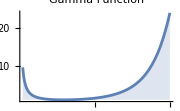

```mathematica
Plot[Gamma[x],{x,.1,5},
PlotLabel->"Gamma Function",ImageSize->Small]
```

Multivariate Function  - Multiply-Applicable Bivariate Operations

Formally, this appears as a function that takes on two or more arguments.

```mathematica
{Plus[a,b],Plus[a,b,c],Plus[a,b,c,d]}
```

{a+b,a+b+c,a+b+c+d}

```mathematica
{Power[a,b],Power[a,b,c],Power[a,b,c,d]}
```

{a^b,a^(b^c),a^(b^(c^d))}

```mathematica
Dot[{a,b},{c,d}]
```

a c+b d

```mathematica
Dot[{{a,b}},{{c},{d}}]
```

{{a c+b d}}

```mathematica
Dot[{{a,b}},{{c},{d}},{{a,b}}]
```

{{a (a c+b d),b (a c+b d)}}

```mathematica
And[a==a,1+2==3,4-5!=6]
```

True

Multivariate Function - Infix Syntax '~'

https://reference.wolfram.com/language/ref/Infix.html

```mathematica
Dot[{a,b},{c,d}]=={a,b}~Dot~{c,d}
```

True

```mathematica
Join[a,b,c]==a~Join~b~Join~c
```

True

```mathematica
a~Power~b~Plus~c~Power~d~Divide~e~Plus~f~Divide~g
```

(((a^b+c)^d)/e+f)/g

Multivariate Function - Different Roles for (two or more) Different Arguments

```mathematica
𝒯𝒶𝒷ℓℯ[{"D[x^3,x]","D[x^3,y]","D[x^3y^5,x]","D[x^3y^5,y]",
"D[x^3y^5,x,y]","D[x^3y^5,{x,3}]","D[x^3y^5,{x,3},y]","D[x^3y^5,{x,3},{y,5}]"},
{{D[x^3,x],D[x^3,y],D[x^3 y^5,x],D[x^3 y^5,y],
D[x^3 y^5,x,y],D[x^3 y^5,{x,3}],D[x^3 y^5,{x,3},y],D[x^3 y^5,{x,3},{y,5}]}},
{{Right,Left}},All,True]
```

D[x^3,x] | 3 x^2
D[x^3,y] | 0
D[x^3y^5,x] | 3 x^2 y^5
D[x^3y^5,y] | 5 x^3 y^4
D[x^3y^5,x,y] | 15 x^2 y^4
D[x^3y^5,{x,3}] | 6 y^5
D[x^3y^5,{x,3},y] | 30 y^4
D[x^3y^5,{x,3},{y,5}] | 720

Multivariate Function - Extending Univariate Functions with Optional Argument(s)

Formally, this appears as a function that takes on one or more arguments.

```mathematica
𝒯𝒶𝒷ℓℯ[{"Range[12.34]","Range[1.23,12.34,.45]"},{{Range[12.34],Range[1.23,12.34,.45]}},Left,All,True]
```

Range[12.34] | {1,2,3,4,5,6,7,8,9,10,11,12}
Range[1.23,12.34,.45] | {1.23,1.68,2.13,2.58,3.03,3.48,3.93,4.38,4.83,5.28,5.73,6.18,6.63,7.08,7.53,7.98,8.43,8.88,9.33,9.78,10.23,10.68,11.13,11.58,12.03}

Multivariate Function - Mathematical Notation

```mathematica
𝒯𝒶𝒷ℓℯ[{"∂_x x^3","∂_y x^3","∂_x (x^3y^5)","∂_y (x^3y^5)","∂_(x, y) (x^3y^5)","∂_{x, 3} (x^3y^5)","∂_({x, 3}, y) (x^3y^5)","∂_({x, 3}, {y, 5}) (x^3y^5)"},
{{D[x^3, x],D[x^3, y],D[(x^3 y^5), x],D[(x^3 y^5), y],D[(x^3 y^5), x,y],D[(x^3 y^5), {x,3}],D[(x^3 y^5), {x,3},y],D[(x^3 y^5), {x,3},{y,5}]}},
{{Right,Left}},All,True]
```

∂_x x^3 | 3 x^2
∂_y x^3 | 0
∂_x (x^3y^5) | 3 x^2 y^5
∂_y (x^3y^5) | 5 x^3 y^4
∂_(x, y) (x^3y^5) | 15 x^2 y^4
∂_{x, 3} (x^3y^5) | 6 y^5
∂_({x, 3}, y) (x^3y^5) | 30 y^4
∂_({x, 3}, {y, 5}) (x^3y^5) | 720

```mathematica
𝒯𝒶𝒷ℓℯ[{"∫x^nⅆx","∫x^1.23ⅆx","∫_4.56^7.89 x^nⅆx","∫_4.56^7.89 x^1.23ⅆx"},
{{∫x^n ⅆx,∫x^1.23 ⅆx,∫_4.56^7.89 x^n ⅆx,∫_4.56^7.89 x^1.23 ⅆx}},
{{Right,Left}},All,True]
```

∫x^nⅆx | x^(1+n)/(1+n)
∫x^1.23ⅆx | 0.44843 x^2.23
∫_4.56^7.89 x^nⅆx | (-4.56 4.56^n+7.89^(1+n))/(1.+n)
∫_4.56^7.89 x^1.23ⅆx | 31.6742

We do recommend inputting multivariate function in such a mathematical notation (when possible) as an equivalent function call can appear unnecessarily verbose.

```mathematica
{Subtract[Plus[a,b,c],d]==a+b+c-d,
Power[a,Log[b]]==a^Log[b],
Or[True,False]==True||False,
And[a==a,Not[a!=a]]==(a==a&&!a!=a),
D[x^3 y^5,{x,3},{y,5}]==D[(x^3 y^5), {x,3},{y,5}],
Integrate[x^1.23,{x,4.56,7.89}]==∫_4.56^7.89 x^1.23 ⅆx}
```

{True,True,True,True,True,True}

Multivariate Function - Parametric Univariate Function

Even though each of the following cases involves a bivariate function call, mathematically one of the two arguments is generally interpreted as a parameter for a univariate function on the other argument. Here 3 is considered the parameter of a 'take the (...)^th root of' function.

```mathematica
125^(1/3)
```

5

Here 5 is the base (parameter) of the Logarithm function.

```mathematica
Log[5,125]
```

3

Here 12 is the modulus (parameter) of the modular arithmetic expression 12345 ≡ 9 (mod 12), i.e. "12,345 hours from midnight will be a nine o'clock (in this case AM)".

https://reference.wolfram.com/language/ref/Mod.html

```mathematica
Mod[12345,12]
```

9

Multivariate Function - Parametric Specification

Consider a Normal Distribution p.d.f. Even though from a functional programming viewpoint, μ and σ are variables, from a probabilistic modelling perspective, these are considered/referred to as distributional parameters. In particular, a Standard Normal Distribution is one with default parameters μ = 0 and σ = 1.

```mathematica
NormalDistribution[]==NormalDistribution[0,1]
```

True

```mathematica
Module[{μ=3.4,σ=1.5,ν=2},
Plot[
{PDF[NormalDistribution[],x],
PDF[NormalDistribution[μ,σ],x],
PDF[StudentTDistribution[ν],x],
PDF[StudentTDistribution[μ,σ,ν],x]},
{x,μ-5σ,μ+.5σ},
PlotLabels->{
"Normal(0,1)",
StringJoin["Normal(μ=",ToString[μ],",σ=",ToString[σ],")"],
StringJoin["Student(ν=",ToString[ν],")"],
StringJoin["Student(μ=",ToString[μ],",σ=",ToString[σ],",ν=",ToString[ν],")"]}, 
Filling->Axis,ImageSize->Large]]
```

-Graphics-

List/Array Construction

Constructing a List of Numbers

Range[ ] constructs a list of numbers, Because such a list most often begins with 1, omitting the first argument in Range[ ] means 1 is assumed by default.

```mathematica
Range[5]
```

{1,2,3,4,5}

When two arguments are applied, the first is then taken to mean the beginning value of the sequence.

```mathematica
Range[5,19]
```

{5,6,7,8,9,10,11,12,13,14,15,16,17,18,19}

A third argument can be used to specify skipping “stride length”.

```mathematica
Range[5,19,2]
```

{5,7,9,11,13,15,17,19}

In fact, Range[ ] specifications need not even be integers.

```mathematica
Range[1.23,45.6,7.89]
```

{1.23,9.12,17.01,24.9,32.79,40.68}

Constructing a List of Indexed Elements

Table[ ] constructs a list with specified indexed elements.

https://reference.wolfram.com/language/ref/Table.html

```mathematica
Table[i,{i,5}]
Table[i,{i,5,19,2}]
Table[i,{i,1.23,45.6,7.89}]
```

{1,2,3,4,5}

{5,7,9,11,13,15,17,19}

{1.23,9.12,17.01,24.9,32.79,40.68}

Indeed, one can check the following.

```mathematica
{Range[5]==Table[i,{i,5}],
Range[5,19,2]==Table[i,{i,5,19,2}],
Range[1.23,45.6,7.89]==Table[i,{i,1.23,45.6,7.89}]}
```

{True,True,True}

Unlike with Range[ ], however, here indices can come from an enumerated set.

```mathematica
Table[Subscript[a, i],{i,{12,Blue,"Boats"}}]
```

{a_12,a_RGBColor[0, 0, 1],a_Boats}

Indeed, one can check the following.

```mathematica
{Table[i,{i,5}]==Table[i,{i,Range[5]}],
Table[i,{i,5,19,2}]==Table[i,{i,Range[5,19,2]}],
Table[i,{i,1.23,45.6,7.89}]==Table[i,{i,Range[1.23,45.6,7.89]}]}
```

{True,True,True}

In any event, most of the times we are not interested in the value of the indices themselves but the indexed items.

```mathematica
Table[Subscript[a, i],{i,5,9}]
```

{a_5,a_6,a_7,a_8,a_9}

Most useful is the fact that Table[ ] allows calculations to be performed on the indices.

```mathematica
Table[2^i,{i,5,9}]
```

{32,64,128,256,512}

```mathematica
Table[Expand[(a+1)^i],{i,0,4}]//TableForm
```

1
1+a
1+2 a+a^2
1+3 a+3 a^2+a^3
1+4 a+6 a^2+4 a^3+a^4

Table[ ] can be nested. (as seen earlier).

```mathematica
Table[Table[(n!)/(m!(n-m)!),{m,0,n}],{n,0,4}]//TableForm
```

1 |  |  |  | 
1 | 1 |  |  | 
1 | 2 | 1 |  | 
1 | 3 | 3 | 1 | 
1 | 4 | 6 | 4 | 1

Constructing an Array of Indexed Elements

Array[ ] offers an convenient construction for when we wishes to keep nesting list constructions, each level defined with equal length objects. The first argument to Array[ ] is the element nomenclature; the second argument defines the dimension of the outcome.

```mathematica
Array[a,{3}]
```

{a[1],a[2],a[3]}

```mathematica
Array[a,{3,2}]
```

{{a[1,1],a[1,2]},{a[2,1],a[2,2]},{a[3,1],a[3,2]}}

```mathematica
Array[a,{3,2,1}]
```

{{{a[1,1,1]},{a[1,2,1]}},{{a[2,1,1]},{a[2,2,1]}},{{a[3,1,1]},{a[3,2,1]}}}

```mathematica
Array[a,{3,2,1,4}]
```

{{{{a[1,1,1,1],a[1,1,1,2],a[1,1,1,3],a[1,1,1,4]}},{{a[1,2,1,1],a[1,2,1,2],a[1,2,1,3],a[1,2,1,4]}}},{{{a[2,1,1,1],a[2,1,1,2],a[2,1,1,3],a[2,1,1,4]}},{{a[2,2,1,1],a[2,2,1,2],a[2,2,1,3],a[2,2,1,4]}}},{{{a[3,1,1,1],a[3,1,1,2],a[3,1,1,3],a[3,1,1,4]}},{{a[3,2,1,1],a[3,2,1,2],a[3,2,1,3],a[3,2,1,4]}}}}

Constructing a List of Pairwise Couplings

Thread[ ] forms a "one-to-one" correspondence between elements from two lists (with same number of elements, of course), using any kind of "connector".

```mathematica
Module[{x={Subscript[a, 1],Subscript[a, 2],Subscript[a, 3]},y={Subscript[b, 1],Subscript[b, 2],Subscript[b, 3]}},
Grid[{
Style[#,Bold,RGBColor[0, 0, 1]]&/@{"x","y","Thread[{x,y}]"},
{x,y,Thread[{x,y}]},
Style[#,Bold,RGBColor[0, 0, 1]]&/@{"Thread[x+y]","Thread[x/y]","Thread[x^2-y^2]"},
{Thread[x+y],Thread[x/y],Thread[(x+y)(x-y)//Expand]},
Style[#,Bold,RGBColor[0, 0, 1]]&/@{"Thread[x^y]","Thread[Log[x,y]","Thread[x->y]"},
{Thread[x^y],Thread[Log[x,y]],Thread[x->y]}},Frame->All]]
```

x | y | Thread[{x,y}]
{a_1,a_2,a_3} | {b_1,b_2,b_3} | {{a_1,b_1},{a_2,b_2},{a_3,b_3}}
Thread[x+y] | Thread[x/y] | Thread[x^2-y^2]
{a_1+b_1,a_2+b_2,a_3+b_3} | {a_1/b_1,a_2/b_2,a_3/b_3} | {a_1^2-b_1^2,a_2^2-b_2^2,a_3^2-b_3^2}
Thread[x^y] | Thread[Log[x,y] | Thread[x->y]
{a_1^b_1,a_2^b_2,a_3^b_3} | {Log[b_1]/Log[a_1],Log[b_2]/Log[a_2],Log[b_3]/Log[a_3]} | {a_1→b_1,a_2→b_2,a_3→b_3}

Association

https://reference.wolfram.com/language/ref/Association.html

An association is essentially a look-up table, whereby each "key" is used to access a particular "value". An association is notated, and indeed can be directly defined, using a special bracket and arrow notation:  '<| key_1 → value_1, key_2 → value_2, ... |>'.

```mathematica
<|"R"->Red,"G"->Green,"B"->Blue,"B"->Green|>
```

<|R→RGBColor[1, 0, 0],G→RGBColor[0, 1, 0],B→RGBColor[0, 1, 0]|>

```mathematica
rgbAssociation=<|"R"->Red,"G"->Green,"B"->Blue|>
```

<|R→RGBColor[1, 0, 0],G→RGBColor[0, 1, 0],B→RGBColor[0, 0, 1]|>

For convenience, keys and values are listed via function Keys[ ] and Values[ ], respectively.

```mathematica
rgbKeys=Keys[rgbAssociation]
rgbValues=Values[rgbAssociation]
```

{R,G,B}

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

https://reference.wolfram.com/language/ref/AssociationThread.html

Conversely, AssociationThread[ ] takes a list of keys and a list of values (assuming same number of elements) and produce an association object.

```mathematica
AssociationThread[rgbKeys,rgbValues]
```

<|R→RGBColor[1, 0, 0],G→RGBColor[0, 1, 0],B→RGBColor[0, 0, 1]|>

Note how this relates to, but differs from, using "plain old" Thread[ ] supplied with "arrow" connector.

```mathematica
Thread[rgbKeys->rgbValues]
```

{R→RGBColor[1, 0, 0],G→RGBColor[0, 1, 0],B→RGBColor[0, 0, 1]}

Indeed, one can go back and forth using Association[ ] and Normal[ ].

```mathematica
Association@Thread[rgbKeys->rgbValues]==AssociationThread[rgbKeys,rgbValues]&& 
Normal@AssociationThread[rgbKeys,rgbValues]==Thread[rgbKeys->rgbValues]
```

True

Note: association is fundamentally a function, and so the correspondence can be "many-to-one" but not "one-to-many" (which is a form of contradiction, whence to be resolved by keeping the last correspondence), while a list of arrow-connected items is essentially a record, and so allows for multiple, even contradictory, versions of the correspondences.

```mathematica
emotionRecord={"Alice"->"sad","Bob"->"so-so","Alice"->"happy","Bob"->"happy","Alice"->"happy","Bob"->"so-so"}
TableForm@Normal@Counts@emotionRecord
```

{Alice→sad,Bob→so-so,Alice→happy,Bob→happy,Alice→happy,Bob→so-so}

(Alice→sad)→1
(Bob→so-so)→2
(Alice→happy)→2
(Bob→happy)→1

```mathematica
emotionLatest=Association@emotionRecord
TableForm@Normal@Counts@Normal@emotionLatest
```

<|Alice→happy,Bob→so-so|>

(Alice→happy)→1
(Bob→so-so)→1

```mathematica
Clear[rgbKeys,rgbValues,emotionRecord,emotionLatest]
```

For data analytics in general, supervised learning in particular, the arrow connector is most frequently used to prepare prediction/regression data into input/output format.

For example, suppose we have weight (in kilogram) and height (in meter) of 6 individuals and whether each has diabetes. Note how "1-to-many correspondences" are allowed, whence two individuals with identical inputs (weight and height readings) may have different output labels.

```mathematica
dataWeightHeight=
{{71,1.7,"M"},{71,1.7,"M"},{72,1.6,"M"},
{55,1.8,"F"},{66,1.7,"F"},{77,1.6,"F"}};
labelDiabetes={"healthy","diabetic","diabetic","healthy","healthy","diabetic"};
dataDiabetesIO=Thread[dataWeightHeight->labelDiabetes]
```

{{71,1.7,M}→healthy,{71,1.7,M}→diabetic,{72,1.6,M}→diabetic,{55,1.8,F}→healthy,{66,1.7,F}→healthy,{77,1.6,F}→diabetic}

Note how AssociationThread[ ] would have eliminated the first data point as the next sample happens to have the same input values (this is not what we would want).

```mathematica
AssociationThread[dataWeightHeight->labelDiabetes]//Normal
```

{{71,1.7,M}→diabetic,{72,1.6,M}→diabetic,{55,1.8,F}→healthy,{66,1.7,F}→healthy,{77,1.6,F}→diabetic}

As a general rule, use Thread[ ] to prepare "I/O" data, but be sure to use AssociationThread[ ] for implementing a "deterministic rule" (as per mathematical notion of function).

For example, a Body Mass Indicator (BMI) calculator is a function, so suppose we are given readings on actual samples (but did not know how BMI is calculated), Thread[ ] would keep redundancies, but AssociationThread[ ] would not (hence presenting a "cleaner" summary)

```mathematica
labelBMI=Which[
#[[1]]/(#[[2]])^2<18.5,"underweight",
#[[1]]/(#[[2]])^2<25,"healthy weight",
#[[1]]/(#[[2]])^2<30,"overweight",
True,"obese"]&/@dataWeightHeight;
```

```mathematica
Grid[Prepend[
{{Thread[dataWeightHeight->labelBMI]//TableForm,
AssociationThread[dataWeightHeight,labelBMI]//Normal//TableForm}},
Style[#,Bold,RGBColor[0, 0, 1]]&/@{"Thread[ ]","AssociationThread[ ]"}],
Alignment->Bottom,Frame->All]
```

Thread[ ] | AssociationThread[ ]
{71,1.7,M}→healthy weight
{71,1.7,M}→healthy weight
{72,1.6,M}→overweight
{55,1.8,F}→underweight
{66,1.7,F}→healthy weight
{77,1.6,F}→obese | {71,1.7,M}→healthy weight
{72,1.6,M}→overweight
{55,1.8,F}→underweight
{66,1.7,F}→healthy weight
{77,1.6,F}→obese

```mathematica
Clear[dataWeightHeight,labelDiabetes,dataDiabetesIO,labelBMI]
```

Useful Operations on/using List/Association

https://reference.wolfram.com/language/ref/Counts.html

Counts[ ] produces an association, its keys corresponding to the patterns, its values corresponding to how often respective patterns appear in the list.

```mathematica
Counts[{1,2,1,2,3,2,1,2,3,4,3,2,1,2,3,4,5,4,3,2,1}]
```

<|1→5,2→7,3→5,4→3,5→1|>

https://reference.wolfram.com/language/ref/Map.html

Maps[ ] applies an action/function/operator (supplied as the first argument) to elements of a list (supplied as the second argument) as its objects/variables/operands.

```mathematica
Map[Length,{{1,2},{3,2,1},{1,2,3,4}}]
Map[Total,{{1,2},{3,2,1},{1,2,3,4}}]
```

{2,3,4}

{3,6,10}

Moreover, with Map[ ], a association can be constructed by applying a function to an already-defined association; the specified operation will be applied to the values fields, keeping the keys in tact.

```mathematica
Map[Length,<|"a"->{1,2},"b"->{3,2,1},"c"->{1,2,3,4}|>]
Map[Total,<|"a"->{1,2},"b"->{3,2,1},"c"->{1,2,3,4}|>]
Map[Lighter,rgbAssociation]
Map[Darker,rgbAssociation]
```

<|a→2,b→3,c→4|>

<|a→3,b→6,c→10|>

<|R→RGBColor[1, Rational[1, 3], Rational[1, 3]],G→RGBColor[Rational[1, 3], 1, Rational[1, 3]],B→RGBColor[Rational[1, 3], Rational[1, 3], 1]|>

<|R→RGBColor[Rational[2, 3], 0, 0],G→RGBColor[0, Rational[2, 3], 0],B→RGBColor[0, 0, Rational[2, 3]]|>

https://reference.wolfram.com/language/ref/Comap.html

Whereas Map[ ] applies an action/function/operator to a list or objects/variables/operands, Comap[ ] lets us apply a list of actions/functions/operators to an object/variable/operand.

```mathematica
Comap[{Length,Total},{1,2,3,4}]
Comap[{Lighter,Darker},RGBColor[0, 0, 1]]
```

{4,10}

{RGBColor[Rational[1, 3], Rational[1, 3], 1],RGBColor[0, 0, Rational[2, 3]]}

https://reference.wolfram.com/language/ref/Prepend.html

https://reference.wolfram.com/language/ref/Append.html

Prepend[ ] and Append[ ] are used to attach an element at the front or the back, respectively, of an existing list, while Join[ ] is used to merge two lists in the order in which they are listed.

```mathematica
Prepend[{2,3,4,5},1]
Join[{1,2},{3},{4,5}]
Append[{1,2,3,4},5]
```

{1,2,3,4,5}

{1,2,3,4,5}

{1,2,3,4,5}

https://reference.wolfram.com/language/ref/Replace.html

https://reference.wolfram.com/language/ref/ReplaceAll.html

Replace[ ] and ReplaceAll[ ] both replace an instance of matched content (if so matched) based on the rule or a list of rules specified, the difference being that the former is more precise in its application in the sense that by default it only applies replacement rule only to complete expressions, not any subpart thereof.

```mathematica
{Replace[1+a,{a->1,b->2,c->3}],
Replace[1+aa,{a->1,b->2,c->3}],
ReplaceAll[1+a,{a->1,b->2,c->3}],
ReplaceAll[1+aa,{a->1,b->2,c->3}]}
```

{1+a,1+aa,2,1+aa}

https://reference.wolfram.com/language/tutorial/StringsAndCharacters.html

StringCount[ ] counts how many characters in a string (a special type of list, i.e. a list of characters) based on supplied with pattern matching directive.

```mathematica
{StringCount["Jack and Jill went up the hill.","j"],
StringCount["Jack and Jill went up the hill.","J"],
StringCount["Jack and Jill went up the hill.",""],
StringCount["Jack and Jill went up the hill.",_]}
```

{0,2,32,31}

Parenthetically, note that whereas "True" and "False" are strings, True and False are boolean values.

Moreover, strings can be considered nominal-scale variables, hence subject to '==' and '!=' operators.

```mathematica
"Jack"!="Jill"
```

True

StringReplace[ ] goes through a string and replaces each instance of matched content (if any) based on the rule or a list of rules specified.

```mathematica
StringReplace["Jack and Jill went up the hill and enjoyed time in said hill.",{"up"->"down","hill"->"valley"}]
```

Jack and Jill went down the valley and enjoyed time in said valley.

```mathematica
Clear[rgbAssociation]
```

Pure Functions

https://reference.wolfram.com/language/ref/Function.html

In functional programming language in general, and for Mathematica in particular, there are built-in functions and user-defined functions. Often user-defined functions requires many different operations using built-in as well as earlier user-defined functions. In any event, these can be used multiple times throughout the program session.

Occasionally, a programer wants to perform a relatively simple, yet hitherto-undefined, operation. This is where "Pure Functions" come in handy. If, from the programmers' perspective, built-in functions are "never-needed-to-define/use-multiple-times" objects, and user-defined functions are "define-once/use-multiple-times" objects, then pure functions are "define-one/use-once" objects.

Explicit

Pure function, i.e. Function[ ], is defined through the use of variable matching protocol using the symbol '#' to stand in where the variable would go. For a univariate case, this suffices.

```mathematica
Function[a#+b][5]
```

5 a+b

```mathematica
Function[#/Length[#]][{a,b,c}]
```

{a/3,b/3,c/3}

But for multivariate case, '#' is followed by a number indicating the order in which each variable is supplied. Hence for a bivariate function, there would be '#1' and '#2'.

```mathematica
Function[#1+ⅇ^#2][12,34]
```

12+ⅇ^34

Alternatively, a multivariate function can be thought of as a univariate function on a vector (more generally list) object.

```mathematica
Function[#[[1]]+ⅇ^(#[[2]])]@{12,34}
```

12+ⅇ^34

```mathematica
Function[(#[[1]])^(#[[2]])]/@{{2,3},{"denominator",-1},{a+b,c+d},{ⅇ,Log[a]}}
```

{8,1/denominator,(a+b)^(c+d),a}

Implicit

Explicitly citing Function[ ] is fine, but a rather clumsy way of denoting pure function, so an implicit declaration with the symbol '&' to indicate that what came before it should be treated as a pure function, is generally preferred.

```mathematica
a#+b&[5]
```

5 a+b

```mathematica
#/Length[#]&[{a,b,c}]
```

{a/3,b/3,c/3}

```mathematica
#1+ⅇ^#2&[12,34]
```

12+ⅇ^34

```mathematica
#[[1]]+ⅇ^(#[[2]])&@{12,34}
```

12+ⅇ^34

```mathematica
(#[[1]])^(#[[2]])&/@{{2,3},{"denominator",-1},{a+b,c+d},{ⅇ,Log[a]}}
```

{8,1/denominator,(a+b)^(c+d),a}

The equivalence between explicit and implicit declarations can be easily ascertained.

```mathematica
#1+ⅇ^#2&==Function[#1+ⅇ^#2]
#[[1]]+ⅇ^(#[[2]])&==Function[#[[1]]+ⅇ^(#[[2]])]
```

True

True

Pure function comes in especially handy when one has to perform simple re-formatting task on a data table.

```mathematica
TableForm[
#[[4]]<>", "<>#[[2]]<>(#[[5]]/.<|"M"->" (male)","F"->" (female)"|>)&/@{
{"Dr.","Poomjai","","Nacaskul","M"},
{"Mr.","John","Jacob","Smith","M"},
{"Miss","Jane","G.I.","Doe","F"}}]
```

Nacaskul, Poomjai (male)
Smith, John (male)
Doe, Jane (female)

User-defined Functions

www.wolfram.com/language/elementary-introduction/2nd-ed/40-defining-your-own-functions.html

As per functional programming paradigm, The bulk of coding will be in the form of writing user-defined functions. Although in practice user-defined functions will generally involve several steps and so may comprise hundreds, even thousands, of lines of code, the following example depicts a simple "one-liner".

Using pattern matching

This is how user-defined functions are generally written

```mathematica
myFunc1[a_,b_]:=a+ⅇ^b
myFunc1[12,34]
```

12+ⅇ^34

Using default parameter(s)

An easy means by which "high-level" functions effectively hide tedious parameterisation specificities from "first-time" users.

```mathematica
myFunc2[a_,b_:34]:=myFunc1[a,b]
myFunc2[12]
```

12+ⅇ^34

Using pure function

Not the usual method, possibly handy for use with just one-liners.

```mathematica
myFunc3 :=#1+Exp[#2]&
myFunc3[12,34]
```

12+ⅇ^34

Using Replace[ ]

Relies on matching named arguments, rarely seen, rarely used.

```mathematica
myFunc4:=myFunc1[a,b]
myFunc4/.{a->12,b->34}
```

12+ⅇ^34

Restricting Argument Type

```mathematica
myFunc5[a_,b_Integer]:=a+ⅇ^b
{myFunc5[12,34],myFunc5[12,34.]}
```

{12+ⅇ^34,myFunc5[12,34.]}

Note how 'myFunc5' could not execute when '34.' is supplied where an Integer is expected.

```mathematica
myFunc6[s_String]:=StringCount[s,"a"]
{myFunc6["abacadabra"],myFunc6[abacadabra]}
```

{5,myFunc6[abacadabra]}

Likewise 'myFunc6' could only execute when supplied with a String.

```mathematica
myFunc7[l_List]:=Exp/@l
{myFunc7[{12,34}],myFunc7[12,34],myFunc7[12.34]}
```

{{ⅇ^12,ⅇ^34},myFunc7[12,34],myFunc7[12.34]}

Finally 'myFunc7’ could only execute when supplied with a List.

```mathematica
Clear[myFunc1,myFunc2,myFunc3,myFunc4,myFunc5,myFunc6,myFunc7]
```

Defining Scope of Variable Definitions with Module[ ]

Oftentimes one needs to temporarily define global variables, assigning values to them, only to use them once for the needed calculation. Then one better make sure to use Clear[ ] to erase the variable references, so as to not be come "side effects" later on in the program code.

```mathematica
x={1.23,4.56,7.89};
n=Length@x;
mean=Mean@x;
meanDevSq=(x-mean)^2;
variance=Total@meanDevSq/(n-1);
stDev=Sqrt@variance;
mean/stDev
```

1.36937

```mathematica
Clear[x,n,mean,meanDevSq,variance,stDev]
```

A better practice is to wrap the local variable definition and whatever calculation is necessary using Module[ ].

https://reference.wolfram.com/language/ref/Module.html

```mathematica
Module[{x={1.23,4.56,7.89},n,mean,meanDevSq,variance,stDev},
n=Length@x;
mean=Mean@x;
meanDevSq=(x-mean)^2;
variance=Total@meanDevSq/(n-1);
stDev=Sqrt@variance;
mean/stDev]
```

1.36937

Also, most of the time, user-defined functions will involve many steps. These steps are separated by ';', the whole of which are then wrapped with '{' at the beginning and '}' at the end.

A better practice is to wrap the entire content of function definition within a Module[ ] construction, which is particular useful as it conveniently allows locally-defined variables that will expire upon execution (whence the function does not leave any so-called "side effect" that would require "cleaning up" later on). These local variables appear in green to indicate their limited scope of definition.

```mathematica
signal2noise[x_]:=
Module[{n,mean,meanDevSq,variance,stDev},
n=Length@x;
mean=Mean@x;
meanDevSq=(x-mean)^2;
variance=Total@meanDevSq/(n-1);
stDev=Sqrt@variance;
mean/stDev]
signal2noise[{1.23,4.56,7.89}]
```

1.36937

```mathematica
Clear[signal2noise]
```

Function Shorthand

'+=' is shorthand setting the left-hand-side to its original value plus the right-hand-side. Likewise for minus, multiply, and divide.

```mathematica
{a=3,a+=9,a-=2,a*=8,a/=6}
```

{3,12,10,80,40/3}

'/@' is shorthand for '~Map~', which itself is the infix form of the function Map[ ].

```mathematica
f/@{x,y,z}
%==f~Map~{x,y,z}==Map[f,{x,y,z}]
```

{f[x],f[y],f[z]}

True

```mathematica
Exp/@{x,y,z}
%==Exp~Map~{x,y,z}==Map[Exp,{x,y,z}]
```

{ⅇ^x,ⅇ^y,ⅇ^z}

True

```mathematica
#^2&/@{x,y,z}
%==(#^2&~Map~{x,y,z})==Map[#^2&,{x,y,z}]
```

{x^2,y^2,z^2}

True

Notice the difference between mapping a function to a list of argument vs. mapping an argument to a list of function! The former sees regular use, while the latter is rarely seen, albeit it can be quite convenient, for example, when comparing different treatments on or properties of the same data set.

```mathematica
𝒯𝒶𝒷ℓℯ[{"data","Mean","GeometricMean","HarmonicMean"},
{N@#@Range@9&/@{Part,Mean,GeometricMean,HarmonicMean}}]
```

data | Mean | GeometricMean | HarmonicMean
{1.,2.,3.,4.,5.,6.,7.,8.,9.} | 5. | 4.14717 | 3.18137

```mathematica
𝒯𝒶𝒷ℓℯ[{"data","MeanDeviation","StandardDeviation","InterquartileRange"},
{N@#@Range@9&/@{Part,MeanDeviation,StandardDeviation,InterquartileRange}}]
```

data | MeanDeviation | StandardDeviation | InterquartileRange
{1.,2.,3.,4.,5.,6.,7.,8.,9.} | 2.22222 | 2.73861 | 4.5

'@@' is shorthand for '~Apply~', which itself is the infix form of the function Apply[ ].

```mathematica
f@@{x,y,z}
%==f~Apply~{x,y,z}==Apply[f,{x,y,z}]
```

f[x,y,z]

True

```mathematica
Plus@@{x,y,z}
%==Plus~Apply~{x,y,z}==Apply[Plus,{x,y,z}]
```

x+y+z

True

```mathematica
5^3==Power[5,3]==Power@@{5,3}==Power~Apply~{5,3}==Apply[Power,{5,3}]==125
```

True

```mathematica
Log[5,125]==Log@@{5,125}==Log~Apply~{5,125}==Apply[Log,{5,125}]==3
```

True

'/.' is shorthand for '~ReplaceAll~’, which itself is the infix form of the function ReplaceAll[ ].

```mathematica
{a,b,c,d,e}/.{a->1,b->2,c->3}
%=={a,b,c,d,e}~ReplaceAll~{a->1,b->2,c->3}==ReplaceAll[{a,b,c,d,e},{a->1,b->2,c->3}]
```

{1,2,3,d,e}

True

'<>' is shorthand for '~StringJoin~', which itself is the infix form of the function StringJoin[ ].

```mathematica
"Jack and Jill"<>" went up "<>"the hill."
%=="Jack and Jill"~StringJoin~" went up "~StringJoin~"the hill."==StringJoin["Jack and Jill"," went up ","the hill."]
```

Jack and Jill went up the hill.

True

```mathematica
Clear[a]
```

Handling Tabular Data with Dataset[ ]

https://reference.wolfram.com/language/guide/ComputationWithStructuredDatasets.html

Dataset[ ] leverages the use of association to create a powerful representation of structured data.

Consider the following nested definitions, from list of arrow-coupled pairs to association and then to dataset.

```mathematica
trafficLightsDataset=Dataset[
trafficLightsAssociation=Association[
trafficLightsListPairs={"STOP"->RGBColor[1, 0, 0],"CAUTION"->RGBColor[1, 1, 0],"GO"->RGBColor[0, 1, 0]}]];
𝒯𝒶𝒷ℓℯ[{"trafficLightsListPairs","trafficLightsAssociation","trafficLightsDataset"},
{{trafficLightsListPairs,trafficLightsAssociation,trafficLightsDataset}},
{{Right,Left}},All,True]
```

trafficLightsListPairs | {STOP→RGBColor[1, 0, 0],CAUTION→RGBColor[1, 1, 0],GO→RGBColor[0, 1, 0]}
trafficLightsAssociation | <|STOP→RGBColor[1, 0, 0],CAUTION→RGBColor[1, 1, 0],GO→RGBColor[0, 1, 0]|>
trafficLightsDataset |

Conversely we can use Normal[ ] to work our way back from dataset to association and then to list of arrow-coupled pairs.

```mathematica
𝒯𝒶𝒷ℓℯ[{"trafficLightsDataset","Normal@trafficLightsDataset","Normal@Normal@trafficLightsDataset"},
{{trafficLightsDataset,Normal@trafficLightsDataset,Normal@Normal@trafficLightsDataset}},
{{Right,Left}},All,True]
```

trafficLightsDataset | 
Normal@trafficLightsDataset | <|STOP→RGBColor[1, 0, 0],CAUTION→RGBColor[1, 1, 0],GO→RGBColor[0, 1, 0]|>
Normal@Normal@trafficLightsDataset | {STOP→RGBColor[1, 0, 0],CAUTION→RGBColor[1, 1, 0],GO→RGBColor[0, 1, 0]}

```mathematica
Clear[trafficLightsListPairs,trafficLightsAssociation,trafficLightsDataset]
```

Compared with table (list of lists), dataset is a bit more troublesome to define, but the extra effort pays out when we wish to access different items by criteria.

```mathematica
TableForm[
personnelTable=
{{"#","Name","Age","Job"},
{"1","Poomjai",55,"Data Scientist"},
{"2","John",44,"Programmer"},
{"3","Jane",33,"Data Scientist"}}]
```

# | Name | Age | Job
1 | Poomjai | 55 | Data Scientist
2 | John | 44 | Programmer
3 | Jane | 33 | Data Scientist

```mathematica
personnelDataset=Dataset[
personnelAssociation=<|
1-><|"Name"->"Poomjai","Age"->55,"Job"->"Data Scientist"|>,
2-><|"Name"->"John","Age"->44,"Job"->"Programmer"|>,
3-><|"Name"->"Jane","Age"->33,"Job"->"Data Scientist"|>|>]
```

Notice how much easier it is with dataset.

```mathematica
{Mean@personnelTable[[2;;,3]],
Mean[personnelAssociation[#,"Age"]&/@Range[3]],
Mean@personnelDataset[All,"Age"]}
```

{44,44,44}

```mathematica
{Counts@personnelTable[[2;;,4]],
Counts[personnelAssociation[#,"Job"]&/@Range[3]],
Counts@personnelDataset[All,"Job"]}
```

{<|Data Scientist→2,Programmer→1|>,<|Data Scientist→2,Programmer→1|>,}

```mathematica
Clear[personnelTable,personnelAssociation,personnelDataset]
```

Files & Storage

https://reference.wolfram.com/language/guide/ImportingAndExporting.html

Import[ ] in most cases automatically assign the appropriate handle, for example, when used with an Excel (.xlsx) file, the result is a list of list of list, whereby the 1st index corresponds to 'worksheet', the 2nd index to 'row', and 3rd index to 'column'. If there are l sheets, each with m rows and n columns, Dimensions[ ] would return {l, m, n}. If a given column contains date values, then DateObject[ ] would automatically apply to each cell values, and so on. 2.2. is likewise quite general w.r.t. file types.

Mathematica works with a myriad of file formats beyond the usual alpha-numeric tables, notably those geared towards graphics/audio-visual data.

https://reference.wolfram.com/language/workflowguide/WorkingWithGraphicsImagesAndSounds

Analytical/Computational/Algorithmic Functionalities

https://reference.wolfram.com/language/workflow/FindAllDefinedFunctions.html

Symbolic Computation Engine

https://reference.wolfram.com/language/tutorial/SymbolicCalculations.html

```mathematica
𝒯𝒶𝒷ℓℯ[{"StandardForm","InputForm","TraditionalForm"},
{{Limit[((x+Δ)^n-x^n)/Δ,Δ->∞],lim_(Δ->∞) ((x+Δ)^n-x^n)/Δ//InputForm,Limit[((x+Δ)^n-x^n)/Δ,Δ->∞]//TraditionalForm},
{Integrate[s[t],{t,a,b}],∫_a^b s[t]ⅆt//InputForm,Integrate[s[t],{t,a,b}]//TraditionalForm}},Left]
```

StandardForm | InputForm | TraditionalForm
ConditionalExpression[∞, (x^n|x)∈ℝ&&n>1] | ConditionalExpression[0, Element[x^n | x, Reals] && Inequality[0, Less, n, Less, 1]] | ConditionalExpression[∞, (x^n|x)∈ℝ∧n>1]
∫_a^b s[t]ⅆt | Integrate[s[t], {t, a, b}] | ∫_a^b s(t)ⅆt

```mathematica
lim_(Δ->0) ((x+Δ)^1.23-x^1.23)/Δ
```

1.23 x^0.23

```mathematica
∑_(i=0)^∞ (-1)^i x^(2i+1)/((2i+1)!)
```

Sin[x]

```mathematica
∑_(i=0)^∞ (-1)^i x^(2i)/((2i)!)
```

Cos[x]

```mathematica
∑_(i=1)^∞ 1/i^2
```

π^2/6

```mathematica
∑_(i=1)^∞ ∑_(j=1)^i 1/(j^2(i+1)^2)
```

π^4/120

```mathematica
∏_(i=1)^∞ (2i)/(2i-1)(2i)/(2i+1)
```

π/2

```mathematica
∫_2^∞ 3 ⅇ^(-3t)ⅆt==Probability[x>2,x\[Distributed]ExponentialDistribution[3]]
```

True

```mathematica
∫_(-∞)^0 PDF[NormalDistribution[],x]ⅆx
```

1/2

Analytical Computation Engine

Consider, for instance, the following (in)famous Borwein integral, which would not be computable under general programming language, e.g. C and Python, which does not come equipped with analytical capability. Numerically, it would be virtually impossible to distinguish exactly π to approximately π, as any numerical computation would almost surely equate 467807924713440738696537864469/467807924720320453655260875000 to 1!

https://en.wikipedia.org/wiki/Borwein_integral

```mathematica
Module[{n=8},
𝒯𝒶𝒷ℓℯ[{"n","∏_(i = 0)^n Sin[FractionBox[x, 2  i + 1]]/(x/(2  i + 1))","∫_(-∞)^∞ ∏_(i = 0)^n Sin[FractionBox[x, 2  i + 1]]/(x/(2  i + 1))ⅆx"},
Transpose@{
Range[n],
TraditionalForm[∏_(i=0)^# Sin[x/(2i+1)]/(x/(2i+1))]&/@Range[n],
∫_(-∞)^∞ (∏_(i=0)^# Sin[x/(2i+1)]/(x/(2i+1)))ⅆx&/@Range[n]}]]
```

n | ∏_(i = 0)^n Sin[FractionBox[x, 2  i + 1]]/(x/(2  i + 1)) | ∫_(-∞)^∞ ∏_(i = 0)^n Sin[FractionBox[x, 2  i + 1]]/(x/(2  i + 1))ⅆx
1 | (3 sin(x/3) sin(x))/x^2 | π
2 | (15 sin(x/5) sin(x/3) sin(x))/x^3 | π
3 | (105 sin(x/7) sin(x/5) sin(x/3) sin(x))/x^4 | π
4 | (945 sin(x/9) sin(x/7) sin(x/5) sin(x/3) sin(x))/x^5 | π
5 | (10395 sin(x/11) sin(x/9) sin(x/7) sin(x/5) sin(x/3) sin(x))/x^6 | π
6 | (135135 sin(x/13) sin(x/11) sin(x/9) sin(x/7) sin(x/5) sin(x/3) sin(x))/x^7 | π
7 | (2027025 sin(x/15) sin(x/13) sin(x/11) sin(x/9) sin(x/7) sin(x/5) sin(x/3) sin(x))/x^8 | (467807924713440738696537864469 π)/467807924720320453655260875000
8 | (34459425 sin(x/17) sin(x/15) sin(x/13) sin(x/11) sin(x/9) sin(x/7) sin(x/5) sin(x/3) sin(x))/x^9 | (17708695183056190642497315530628422295569865119 π)/17708695394150597647449176493763755467520000000

https://reference.wolfram.com/language/ref/Factor.html

Factor[ ] takes apart polynomials.

```mathematica
Module[{expression=Expand[(x+1)(2x-3)(4x+5)(6x-7)(8x+9)]},
𝒯𝒶𝒷ℓℯ[{"5th order polynomial","its factorisation"},
{{expression,Factor[expression]}},{{Right,Left}},All,True]]
```

5th order polynomial | 945+1101 x-1064 x^2-1332 x^3+272 x^4+384 x^5
its factorisation | (1+x) (-3+2 x) (5+4 x) (-7+6 x) (9+8 x)

```mathematica
Module[{expression=Expand[(a+b)^8]},
𝒯𝒶𝒷ℓℯ[{"5th order polynomial","its factorisation"},
{{expression,Factor[expression]}},{{Right,Left}},All,True]]
```

5th order polynomial | a^8+8 a^7 b+28 a^6 b^2+56 a^5 b^3+70 a^4 b^4+56 a^3 b^5+28 a^2 b^6+8 a b^7+b^8
its factorisation | (a+b)^8

https://reference.wolfram.com/language/ref/Solve.html

Solve[ ] takes two arguments, the equation(s) expressed in terms of various parameters and variables, and the variables to solve for.

```mathematica
Solve[{{Subscript[a, 11],Subscript[a, 12]},{Subscript[a, 21],Subscript[a, 22]}}.{Subscript[x, 1],Subscript[x, 2]}=={Subscript[b, 1],Subscript[b, 2]},{Subscript[x, 1],Subscript[x, 2]}]
```

{{x_1→-(a_22 b_1-a_12 b_2)/(a_12 a_21-a_11 a_22),x_2→-(-a_21 b_1+a_11 b_2)/(a_12 a_21-a_11 a_22)}}

With numerical coefficients put in, one can see how Solve[ ] deals with case with unique solution ...

```mathematica
Solve[{{1,2},{3,4}}.{Subscript[x, 1],Subscript[x, 2]}=={5,6},{Subscript[x, 1],Subscript[x, 2]}]
```

{{x_1→-4,x_2→9/2}}

... no solution ...

```mathematica
Solve[{{1,2},{2,4}}.{Subscript[x, 1],Subscript[x, 2]}=={5,6},{Subscript[x, 1],Subscript[x, 2]}]
```

{}

... and infinitely many solutions (warning message may appear).

```mathematica
Off[Solve::svars]
Solve[{{1,2},{2,4}}.{Subscript[x, 1],Subscript[x, 2]}=={5,10},{Subscript[x, 1],Subscript[x, 2]}]
On[Solve::svars]
```

{{x_2→5/2-x_1/2}}

Let’s apply this to the task of solving for a stationary points, one of whom corresponds to the global function minimum.

```mathematica
myFunction[x_,y_]:=x^4+2 y^2-5 x^2+10 x y+y/100
```

```mathematica
Plot3D[myFunction[x,y],{x,-4,4},{y,-8,8},
PlotLabel->TraditionalForm@myFunction[x,y],
AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
itsGradient=D[myFunction[x,y], {{x,y}}]
```

{-10 x+4 x^3+10 y,1/100+10 x+4 y}

```mathematica
𝒯𝒶𝒷ℓℯ[{"soln x","soln y"},
Solve[itsGradient=={0,0},{x,y}],Left]
```

soln x | soln y
x→ | y→1/400 (-1-1000 )
x→ | y→1/400 (-1-1000 )
x→ | y→1/400 (-1-1000 )

As Solve[ ] is expressed in analytical form, we apply N[ ] to obtain the numerical values, .

```mathematica
𝒯𝒶𝒷ℓℯ[{"soln x","soln y"},
N/@Solve[itsGradient=={0,0},{x,y}],Left]
```

soln x | soln y
x→-2.95768 | y→7.39171
x→-0.000714286 | y→-0.000714286
x→2.9584 | y→-7.39849

Numerical Computation Engine

https://reference.wolfram.com/language/tutorial/NumericalOperationsOnFunctionsOverview.html

NSolve[ ] is the numerical version of Solve[ ].

Let's repeat the above calculation in one step.

```mathematica
myStationaryPt=NSolve[D[(myFunction[x,y]), {{x,y}}]=={0,0},{x,y}]
```

{{x→2.9584,y→-7.39849},{x→-2.95768,y→7.39171},{x→-0.000714286,y→-0.000714286}}

https://reference.wolfram.com/language/ref/NMinimize.html

NMinimize[ ] is the direct way of finding function minimum analytically. It gives the minimum function value, followed by the solution that achieves said minimum.

```mathematica
myFuncMin=NMinimize[myFunction[x,y],{x,y}]
```

{-76.6365,{x→2.9584,y→-7.39849}}

Note that the solution to NMinimize[ ] is one amongst the stationary points obtained in prior step.

```mathematica
MemberQ[myStationaryPt,myFuncMin[[2]]]
```

False

Check that it also has the minimum function values amongst the stationary points.

```mathematica
myFuncMin[[1]]==Min[myFunction[x,y]/.#&/@myStationaryPt]
```

True

```mathematica
Clear[myFunction,itsGradient,myStationaryPt,myFuncMin]
```

Semi-Analytical Computation Engine

https://reference.wolfram.com/language/ref/DSolve.html

DSolve[ ] takes two arguments, the differential equation, along with boundary and initial conditions, expressed in terms of various parameters and variables, and the variables to solve for.

Let's take as an example, the well-known 1-dim Heat (aka Diffusion) Equation, where the 1st derivative w.r.t. time (i.e. how fast a hypothetical heat-conducting rod cools down from initial temperature above its environment) is proportional to the 2nd derivative w.r.t. position (i.e. how drastic a difference in temperature along the length of said rod).

```mathematica
heatEqn=D[u[x,t], t]==1/7 D[D[u[x,t], x], x];
```

Let’s specify the boundary condition w.r.t. the end points (say, the rod registers no temperature differential towards both ends).

```mathematica
boundaryCondi=(D[u[x,t], x]/.x->0)==(D[u[x,t], x]/.x->1)==0;
```

Also specify the initial condition w.r.t. starting time (say, the rod had been heated towards its midpoint).

```mathematica
initialCondi=u[x,0]==2-(x-1/2)^2;
```

Now solve for the solution function. Beware: this may take quite a while, as noted by evaluated Timing[ ].

```mathematica
Timing[solnHeatEqn=DSolve[{heatEqn,boundaryCondi,initialCondi},u[x,t],{x,t}]]
```

{28.9531,{{u[x,t]→23/12+2 -((1+(-1)^K[1]) ⅇ^(-1/7 π^2 t K[1]^2) Cos[π x K[1]])/(π^2 K[1]^2)K[1]1∞}}}

From this semi-analytical (i.e. still apparently closed-form, but now involves an infinite sum) solution function, we can then take an approximation, say, up to 4 terms on the one solution function found in this case (i.e. referenced by '[[1]]'), resulting in the the following simplified expression. (note: Activate[ ] is used here supposedly to rid ourselves of the dummy variable 'K[1]'.)

```mathematica
Simplify[Activate[solnHeatEqn[[1]]/.∞->4]]
```

{u[x,t]→23/12-(ⅇ^(-(4 π^2 t)/7) Cos[2 π x])/π^2-(ⅇ^(-(16 π^2 t)/7) Cos[4 π x])/(4 π^2)}

This solution function can then be stored/named for later use.

```mathematica
heatAlongLengthOverTime[x_,t_]:=Values[Activate[solnHeatEqn[[1]]/.∞->3][[1]]]
```

```mathematica
Plot3D[heatAlongLengthOverTime[x,t],{x,0,1},{t,0,1},
AxesLabel->{"position","time","temperature"}]
```

-Graphics3D-

```mathematica
Clear[heatEqn,boundaryCondi,initialCondi,solnHeatEqn,heatAlongLengthOverTime]
```

```mathematica
NotebookSave[];EmitSound[Sound[SoundNote["C",.5,"Violin"]]]
```

## Glossary

Artificial Intelligence (AI) - the notion that human-like intelligence, behaviours and or responses to stimuli indicative of human intelligence, can be replicated in an artificial apparatus, especially in the form of programmable digital computer. In essence, the I in AI simply means “human like”, regardless or the behaviour/response would be considered “intelligent”, i.e. in terms of accuracy, insights, or problem solving. In other words, an AI system would be considered 100% successful if it can pass itself off as a human being, even a very unintelligent one! The term has since grown to encompass any manifestation of Computational/Digital Intelligence independent (even above and beyond that) of human mimicry.

Business Intelligence (BI) – despite the fact that BI (aka Enterprise Intelligence) often uses AI, the term intelligence in BI is used in a very different sense to how it appears in AI. In fact, BI arose as a business-world analog of Military Intelligence. As such BI has more to do with the quality of information and the ability to translate possession of said information immediately into tangible, actionable insights, rather than the ability to learn from data, form internal model (representation of reality), make associations, infer causalities, recognise patterns, produce predictions, and/or suggest (approximately optimal) courses of actions, which are the primary aims of AI research. However, viewed from a software/system engineering perspective, BI represents an encapsulation/user-interface wrapping of Enterprise Analytics of all kinds, AI-based or otherwise.

Computational Intelligence (CI) – unlike AI, human mimicry is never part of the goal. Here intelligence is judged by the ability to solve problems—finding an answer, finding the best or optimal answer from a space of all possible answers, finding a means to ensure trajectorial stability vis-à-vis a dynamical system, and so on. Three strains of research gained prominence: optimisation by means of computer simulation algorithms inspired by and analogous to the process of genetic-biological evolution by natural selection, i.e. Genetic Algorithm (GA), Genetic Programming (GP), Evolutionary Algorithm (EA), learning by means of computational paradigm inspired by and analogous to the computational architecture and signal processing dynamics of biological brains, i.e. Artificial Neural Network (ANN), and mapping between human concepts and machine representation so as to realise man-machine synergy, i.e. Fuzzy Sets & Systems, Cybernetics, Human-Computer Interaction/Interface).

Digital Intelligence – combining the notion that a digital computer can process/possess knowledge, a la AI, with the notion that digital devices can be endowed with sensory organs, thereby able to gather/generate intelligent information about their surroundings and operating conditions a la Internet of Things (IoT), and so on.

Machine Learning (ML) – can be thought of as a generalisation of the algorithmic calibration of ANN parameters, thereby encompassing a myriad of non-ANN methodologies, whence incorporating a multitude of learning modalities (i.e. Unsupervised Learning, Supervised Learning, Reinforcement Learning, and Representation Learning), cognitive process/knowledge representations, and symbolic/semantic schemas.

Deep Learning (DL) – can be thought of as a modern rebranding of a particular Artificial Neural Network architecture dominant in/since 1980’s, the Multi-Layer Perceptron (MLP). However, DL also distinguishes itself from its 1980’s root by virtue of (i) computational power hitherto unavailable—MLP with more than a handful of layers of perceptrons used to get bogged down and easily overwhelmed by large data set, (ii) algorithmic tweaks that prevent connection weights in ANN architecture with many interconnected and/or self-connected layers of perceptrons from degenerating (going to zero or infinity) during training, and (iii) recent breakthrough in adapting/engineering ANN architecture for image recognition tasks, i.e. Convolutional Neural Network (CNN), temporal models, i.e. Recurrent Neural Network (RNN), and generative Large Language Model (LLM), i.e. Generative Pre-trained Transformer (GPT).

Quantitative Models (QM) – the all-encompassing term in reference to Applied Mathematics, covering everything from a basic linear regression equation, rooting back a few centuries, to the latest DL innovations. It is based on the most undemanding pretext that any entities or phenomena under study can be indirectly studied/analysed, hence modelled, on basis of their quantitative attributes. As “it’s always cheaper to play with the toy than to muck about with the real thing”, modelling entities and phenomena quantitatively saves one from making real mistakes.

Quantitative Analytics (QA) – the engineering and “productionisation” of Quantitative Analysis (from traditional Statistical Inference to ML-based methodologies) into a suite of readily deployable tools. The term also refers to a set of (system) statistics themselves, which are produced, presumably on a regular basis, for the purpose of performance evaluation, fault diagnostics, and managerial review.

Quantitative Analyst – a job description, highlighting the fact that it is the ability to create and work with QA, rather than possession of domain knowledge, that is the critical success factor in practical applications. A “Quant” may find him/herself in an insurance industry one day, defense industry the next, and so on. There is a sort of universality with which problems in insurance and defense industries alike, that can be mapped onto the same/similar mathematical structure, hence analysed using the same/similar QM platforms.

Enterprise Analytics (EA)  – refers to the comprehensive set of QA tools and techniques used in the strategic, tactical, as well as routine management of an enterprise, especially large, for-profit corporations, but also increasingly relevant vis-à-vis small, Network Economy-oriented social enterprises.

Big Data – the term characterising three emergent data trends: (i) sheer volume, (ii) unprecedented velocity with which bits and pieces of data get generated, pass through digital channels, and arrive at depositories, and (iii) the variety of format, especially unstructured data streams comprising images, sound files, and telemetric data logs. Big Data also refers to the premise, or rather the promise, that hidden amongst the volume of high-velocity, multi-variety data lie patterns and nuances that powerful enough Data Mining and ML algorithms can cipher and distill into useful insights, thereby uncovering a new set of information that would otherwise not have been captured by traditional statistics and econometric methods.

Data Mining – refers to the notion that data is a raw material within which precious, useful bits of information lie hidden, and also to the process of distilling a vast amount of data for such precious, useful bits of information, in direct analogy to the process of distilling a vast amount of ores for precious gems. The term has since fallen out of favour due to its association with relatively primitive (by today’s standard) methodologies based essentially on probability look-up tables.

Data Science – the recognition of availability and arrival of Big Data, together with the maturity and utility of our ability to engineer powerful QM to analyse them. Moreover, there is an emergent area of scientific investigation that study to very dynamics of data objects (be it data bases, network connectivities, texts and contextual data objects, etc.), how they get generated, evolve, travel/propagate, and meet their ultimate fate (do bits of data die, or do they live forever?). Data Science is essentially an empirical science. With the theoretical foundation (i.e. that data contains information about system behaviours that can be quantitatively modelled partially predicted, and so on) having been worked out, it remains a matter of experiments to determine which amongst the myriad of QA tools and techniques available best model a particular system whose behaviours have been captured in data records.

Data Scientist – either someone who is dedicated to the career of researching Data Science proper, or more commonly a (presumably very good) Quantitative Analyst who heads a top-notch QA team.

Internet of Things (IoT) – the enhancement of mechanical-electrical devices with ability to gather, process, generate, store, and report digitally-formatted data and communicate them (nearly) live via the internet to the intended (sometimes unintended) users.

Network Economy – firstly refers to the extent to which modern economy is driven by and dependent upon the internet, but latterly refers to the phenomenon by which—as a direct and indirect result of internet becoming ubiquitous in our daily lives—people, city inhabitants, households, economic production/consumption units, and so on, begin to interact and relate to one another based on technology-enabled network topology rather than on the basis of physical proximities, geographic localities, or even familial ties.

Digital Economy – overlaps with the notion of Network Economy, with perhaps stronger emphasis on the prevalence of digital devices as key aspects of human productivity, digital communications as key modes of human connectivity, and digital contents surpassing all other form of archives in human history.

## Biography

Poomjai Nacaskul received his Bachelor of Arts (BA) degree cum laude in Physics and Economics (double majors) from Western Reserve College, Case Western Reserve University (CWRU) in 1992, a Master of Science degree in Operations Research (w/ minor in Finance) from CWRU’s Weatherhead School of Management in 1993, and a Doctor of Philosophy in Computational Intelligence and Operational Research from Imperial College of Science, Technology and Medicine, then part of the University of London system, in 1998. Whilst at Imperial, Poomjai also interned as Quantitative Analyst with Chemical Bank/Chase Manhattan Bank (UK)’s Quantitative Research and Trading (QRT) unit, where he developed object-oriented evolutionary optimisation programme for the ‘prop desk’ to optimise high-frequency foreign-exchange trading and model portfolio.

Upon graduation from Imperial College in 1998, Poomjai began his career as an Investment Officer with the Bank of Thailand (BOT)’s International Reserves Management team, during which time he also passed Level I, Level II, and Level III Certified Financial Analyst (CFA) examinations. After a stint at BOT’s London Representative Office and being attached to the Basel II Capital Adequacy: Internal Ratings-Based (IRB) Approach programme, Poomjai went on to create BOT’s first Quantitative Models and Financial Engineering (QMFE) team with BOT’s Financial Institutions Policy Group, eventually graduating to the Principal Researcher position with BOT’s Monetary Policy Group. At BOT, Poomjai researched and developed cutting-edge analytics, from Relative Numeraire Risk in Multi-Currency Portfolio to Copula Modelling in Pricing Credit Derivatives, and Eigenvector Centrality Identification of Systemically Important Financial Institutions.

Poomjai joined Siam Commercial Bank (SCB) as First Senior Vice President, Head of Credit Risk Analytics in 2013 and subsequently created the bank’s first Quantitative Models and Enterprise Analytics (QMEA) unit, subsequently incorporated into SCB’s Business Intelligence/Data Analytics function in 2017, and became one of the bank’s first dedicated Lead/Principal Data Scientists. At SCB, Poomjai’s involvements reached beyond credit risk, ranging from Predictive Analytics (hourly branch-level customer queue prediction) to Financial Engineering (validation of Vanna-Volga method for pricing FX exotic derivatives), and Network Flow Modelling (intra/extra-SCB flows of wholesale liquidity funding).

He presently holds a academic (lecturing) position as Faculty of Applied Digital Intelligence with Chulalongkorn School of Integrated Innovation (CSII)’s Bachelor of Arts and Science in Integrated Innovation (BAScii) international programme, and remains active as private Data Science consultant, notably with UOB Asset Management (Thailand) and Banpu PCL, as well as Thailand’s Revenue Department and the Office of Small and Medium Enterprises Promotion (the latter two in conjunction with Business On Line PCL).
Apart from Risk Management, Quantitative Finance, Data Science, Machine Learning, and Artificial Intelligence, Poomjai has keen research interest in the Sufficiency Economy Philosophy as paradigmatic solution framework vis-à-vis global/domestic Sustainable Development challenges.

-Graphics-

-Graphics-